# Verification of the manuscript QCLT, version 29

## A feedback-driven central limit theorem with q-Gaussian limits: checks of the calculations, tables and figures

This notebook checks the calculations of the manuscript "A feedback-driven central limit theorem with q-Gaussian limits" (G. B. Bagci and T. Oikonomou) and redraws its tables and figures. Equation, section, lemma, table and figure numbers are those of the manuscript: Eqs. (II.1)-(II.7) in Sec. II, (III.1)-(III.5) in Sec. III, (IV.1)-(IV.7) in Sec. IV, (V.1)-(V.4) in Sec. V, (A.1)-(A.10) in Appendix A and (B.1)-(B.2) in Appendix B; Tables I-III; Figures 1-3. Checks marked additional concern intermediate quantities that the manuscript does not tabulate. Every check prints PASS or FAIL when it is evaluated, and Section 11 collects all of them in one table.

How to run: Evaluation > Evaluate Notebook. Sections 0 to 5 and Section 10 are symbolic or exact checks and numerical checks on grids; they take a few minutes in all. Section 6 simulates the recursion (II.1) with the parameters of the manuscript (200000 paths, N = 10000, eleven cases); this takes roughly 10 to 20 minutes. Set mPaths = 20000 in the first cell of Section 6 for a quick run. The random seed is fixed, but the random numbers differ from those of the Python simulation used for the manuscript, so the simulated numbers agree with the manuscript only within sampling error.

Status. Sections 0-9 were run in Mathematica by G. B. Bagci, and all checks passed. For manuscript version 21 the references in the names of the checks and in the comments were changed to the numbering of the manuscript; the code of Sections 0-9 is unchanged. Three checks were added at the end of Section 2 for the paragraph of Sec. II C on the diffusion behind (II.7), and Section 10 (Proposition E, Appendix B) was added. The new checks were run in a Wolfram kernel and passed; they have not yet been run in Mathematica.

What a check can and cannot show. The algebraic identities are verified symbolically or in exact arithmetic. Inequalities that hold for all values of the variables are tested on grids; a pass on a grid is a consistency check, not a proof. Statements that rest on standard theorems (Kolmogorov and Weierstrass theorems, the duality formula for the Wasserstein distance, the existence of optimal couplings, dominated convergence, uniqueness for linear differential equations) are not reproved; the formulas that the proof derives from them are checked.

## 0. Setup: the limit law g_b, the constants and the noise laws

Definitions: kappa, sigma, the normalizing constant Z_b in closed form, g_b, q(b), a_1, Lambda of (IV.4), C_L of (IV.7).

```mathematica
results = <||>;
```

```mathematica
check[name_String, cond_] := Module[{ok = TrueQ[cond]},
   results[name] = ok;
   Row[{Style[If[ok, "PASS", "FAIL"], Bold, If[ok, Darker[Green], Red]], "   ", name}]];
```

```mathematica
close[x_, y_, tol_ : 10^-8] := Abs[N[x] - N[y]] <= tol Max[1, Abs[N[y]]];
```

```mathematica
kap[b_] := 1 + 1/(2 b);
```

```mathematica
sig[y_, b_, c_] := Sqrt[c + b y^2];
```

```mathematica
zz[b_, c_] := If[b > 0, c^(1/2 - kap[b]) Sqrt[Pi/b] Gamma[kap[b] - 1/2]/Gamma[kap[b]],
   c^(1/2 - kap[b]) Sqrt[-Pi/b] Gamma[1 - kap[b]]/Gamma[3/2 - kap[b]]];
```

```mathematica
gb[y_, b_, c_] := If[b > 0 || y^2 < -c/b, (c + b y^2)^(-kap[b])/zz[b, c], 0];
```

```mathematica
qOf[b_] := (1 + 4 b)/(1 + 2 b);
```

```mathematica
a1Of[b_, c_] := Sqrt[c] Gamma[kap[b] - 1] Gamma[kap[b]]/Gamma[kap[b] - 1/2]^2;
```

```mathematica
lamOf[b_, m3_] := Exp[4 Sqrt[2] b^(3/2) m3 (Zeta[3/2] - 1)];
```

```mathematica
clOf[b_, c_, m3_] := a1Of[b, c] m3 (33 + 83 b/2 + 6/b);
```

```mathematica
atoms["rademacher"] = {{1, 1/2}, {-1, 1/2}};
```

```mathematica
atoms["two"] = {{2, 1/5}, {-1/2, 4/5}};
```

```mathematica
atoms["three"] = {{-Sqrt[2], 1/4}, {0, 1/2}, {Sqrt[2], 1/4}};
```

```mathematica
m3["rademacher"] = 1; m3["two"] = 17/10; m3["gauss"] = 2 Sqrt[2/Pi]; m3["exp"] = 12/E - 2;
```

```mathematica
colB = RGBColor[0.165, 0.471, 0.839]; colO = RGBColor[0.922, 0.408, 0.204]; colA = RGBColor[0.106, 0.686, 0.478];
```

## 1. Sec. II A: the statement (Eqs. II.1-II.4 and Table I)

(II.2): the normalising constant and the limit law

```mathematica
zNum[b_, c_] := If[b > 0, NIntegrate[(c + b y^2)^(-kap[b]), {y, -Infinity, Infinity}], NIntegrate[(c + b y^2)^(-kap[b]), {y, -Sqrt[-c/b], Sqrt[-c/b]}]];
```

```mathematica
check["(II.2): closed form of Z_b equals the integral of D^(-kappa) (b = 1/3, 1, 2, -1/4, -1/2, -1; c = 1, 23/10)",
  And @@ Flatten@Table[close[zz[b, c], Quiet@zNum[b, c], 10^-5], {b, {1/3, 1, 2, -1/4, -1/2, -1}}, {c, {1, 23/10}}]]
```

PASS   (II.2): closed form of Z_b equals the integral of D^(-kappa) (b = 1/3, 1, 2, -1/4, -1/2, -1; c = 1, 23/10)

(II.3): the q-Gaussian form

```mathematica
check["(II.3): (1-q) B = -b/c and 1/(1-q) = -kappa, with q = (1+4b)/(1+2b) and B = (1+2b)/(2c)",
  Simplify[(1 - qOf[b]) (1 + 2 b)/(2 c) == -b/c] && Simplify[1/(1 - qOf[b]) == -kap[b]]]
```

PASS   (II.3): (1-q) B = -b/c and 1/(1-q) = -kappa, with q = (1+4b)/(1+2b) and B = (1+2b)/(2c)

```mathematica
check["(II.3): inverse relation b = (q-1)/(2(2-q))", Simplify[(qOf[b] - 1)/(2 (2 - qOf[b])) == b]]
```

PASS   (II.3): inverse relation b = (q-1)/(2(2-q))

```mathematica
check["Sec. II A: g_b is proportional to [1-(1-q) B y^2]^(1/(1-q)) (the ratio does not depend on y)",
  And @@ Flatten@Table[With[{q = qOf[b], bq = (1 + 2 b)/(2 c)}, close[gb[y, b, c]/(1 - (1 - q) bq y^2)^(1/(1 - q)), gb[0, b, c], 10^-10]],
    {b, {1/3, 1, 2, -1/4, -1/3}}, {c, {1, 23/10}}, {y, {1/5, 1/2, 9/10}}]]
```

PASS   Sec. II A: g_b is proportional to [1-(1-q) B y^2]^(1/(1-q)) (the ratio does not depend on y)

```mathematica
check["Sec. II A: for b > 0, g_b is the law of Sqrt[c/(1+b)] T with T a Student variable with 1 + 1/b degrees of freedom",
  And @@ Flatten@Table[close[gb[y, b, c], PDF[StudentTDistribution[0, Sqrt[c/(1 + b)], 1 + 1/b], y], 10^-10], {b, {1/3, 1, 2}}, {c, {1, 23/10}}, {y, {-7/2, -1, 0, 1/3, 5}}]]
```

PASS   Sec. II A: for b > 0, g_b is the law of Sqrt[c/(1+b)] T with T a Student variable with 1 + 1/b degrees of freedom

```mathematica
check["Sec. II A: for b < 0, g_b is the law of L(2V-1) with V a Beta(1/(2|b|), 1/(2|b|)) variable",
  And @@ Flatten@Table[With[{al = -1/(2 b), el = Sqrt[-c/b]}, close[gb[y, b, c], PDF[BetaDistribution[al, al], (y/el + 1)/2]/(2 el), 10^-10]],
    {b, {-1/4, -1/2, -1, -5/2}}, {c, {1, 23/10}}, {y, {-1/2, 0, 1/7, 3/5}}]]
```

PASS   Sec. II A: for b < 0, g_b is the law of L(2V-1) with V a Beta(1/(2|b|), 1/(2|b|)) variable

```mathematica
check["Table I: q(-1/4) = 0, q(1/3) = 7/5, q(1) = 5/3, q(2) = 9/5; kappa(-1/2) = 0 (uniform); kappa(-1) = 1/2 (arcsine)",
  qOf[-1/4] == 0 && qOf[1/3] == 7/5 && qOf[1] == 5/3 && qOf[2] == 9/5 && kap[-1/2] == 0 && kap[-1] == 1/2]
```

PASS   Table I: q(-1/4) = 0, q(1/3) = 7/5, q(1) = 5/3, q(2) = 9/5; kappa(-1/2) = 0 (uniform); kappa(-1) = 1/2 (arcsine)

```mathematica
check["Table I: b = -1 gives the arcsine density 1/(Pi Sqrt[c - y^2]); b = -1/2 gives the uniform density 1/(2L)",
  And @@ Table[close[gb[y, -1, 2], 1/(Pi Sqrt[2 - y^2])] && close[gb[y, -1/2, 2], 1/4], {y, {-1, 0, 1/3, 5/4}}]]
```

PASS   Table I: b = -1 gives the arcsine density 1/(Pi Sqrt[c - y^2]); b = -1/2 gives the uniform density 1/(2L)

```mathematica
varNum[b_, c_] := If[b > 0, NIntegrate[y^2 gb[y, b, c], {y, -Infinity, Infinity}], NIntegrate[y^2 (c + b y^2)^(-kap[b])/zz[b, c], {y, -Sqrt[-c/b], Sqrt[-c/b]}]];
```

```mathematica
check["Table I: the variance of g_b is c/(1-b) for b < 1 (b = 1/3, 1/2, -1/4, -1/2, -1)",
  And @@ Flatten@Table[close[Quiet@varNum[b, c], c/(1 - b), 10^-4], {b, {1/3, 1/2, -1/4, -1/2, -1}}, {c, {1, 23/10}}]]
```

PASS   Table I: the variance of g_b is c/(1-b) for b < 1 (b = 1/3, 1/2, -1/4, -1/2, -1)

(II.1)-(II.4): the recursion

```mathematica
check["(II.4): dividing (II.1) by Sqrt[n+1] gives Y_(n+1) = rho_n Y_n + eps_n sigma(Y_n) xi, and rho_n^2 + eps_n^2 = 1",
  And @@ Flatten@Table[close[(s + Sqrt[c + b s^2/n] x)/Sqrt[n + 1], Sqrt[n/(n + 1)] (s/Sqrt[n]) + sig[s/Sqrt[n], b, c] x/Sqrt[n + 1], 10^-12] && n/(n + 1) + 1/(n + 1) == 1,
    {n, {1, 2, 7, 100}}, {s, {-3/2, 1/5, 2}}, {x, {-1, 2/3}}, {b, {-1/10, 1/3, 2}}, {c, {1, 23/10}}]]
```

PASS   (II.4): dividing (II.1) by Sqrt[n+1] gives Y_(n+1) = rho_n Y_n + eps_n sigma(Y_n) xi, and rho_n^2 + eps_n^2 = 1

## 2. Sec. II C: Lemma 1 (Eq. II.7) and the diffusion behind it

```mathematica
check["(II.7), Lemma 1: (D g_b)' = -y g_b, symbolically in b, c, y",
  Simplify[D[(c + b y^2)^(1 - kap[b]), y] + y (c + b y^2)^(-kap[b])] === 0]
```

PASS   (II.7), Lemma 1: (D g_b)' = -y g_b, symbolically in b, c, y

```mathematica
check["Sec. II C: (II.7) implies (1/2)(D g)'' + (1/2)(y g)' = 0",
  Simplify[D[(c + b y^2) (c + b y^2)^(-kap[b]), {y, 2}]/2 + D[y (c + b y^2)^(-kap[b]), y]/2] === 0]
```

PASS   Sec. II C: (II.7) implies (1/2)(D g)'' + (1/2)(y g)' = 0

```mathematica
check["Lemma 1: D g_b tends to 0 at the ends of I_b (b = 1/3, 1, 2 at infinity; b = -1/4, -1/2, -1 at y = L)",
  And @@ Table[Limit[(1 + b y^2)^(-1/(2 b)), y -> Infinity] == 0, {b, {1/3, 1, 2}}] &&
   And @@ Flatten@Table[((c + b y^2)^(-1/(2 b)) /. y -> Sqrt[-c/b]) == 0, {b, {-1/4, -1/2, -1}}, {c, {1, 23/10}}]]
```

PASS   Lemma 1: D g_b tends to 0 at the ends of I_b (b = 1/3, 1, 2 at infinity; b = -1/4, -1/2, -1 at y = L)

Sec. II C: the diffusion behind (II.7) and the paragraph on recursions of stochastic-approximation type

```mathematica
check["Sec. II C: (II.7) is the zero-current condition of the diffusion dU = -U/2 dt + sigma(U) dW: the probability current -(1/2) y g_b - (1/2)(D g_b)' vanishes identically",
  Simplify[-y (c + b y^2)^(-kap[b])/2 - D[(c + b y^2) (c + b y^2)^(-kap[b]), y]/2] === 0]
```

PASS   Sec. II C: (II.7) is the zero-current condition of the diffusion dU = -U/2 dt + sigma(U) dW: the probability current -(1/2) y g_b - (1/2)(D g_b)' vanishes identically

```mathematica
check["Sec. II C: rho_n = 1 - 1/(2(n+1)) + O(n^-2), since n^2 (rho_n - 1 + 1/(2(n+1))) -> -1/8",
  Limit[n^2 (Sqrt[n/(n + 1)] - 1 + 1/(2 (n + 1))), n -> Infinity] == -1/8]
```

PASS   Sec. II C: rho_n = 1 - 1/(2(n+1)) + O(n^-2), since n^2 (rho_n - 1 + 1/(2(n+1))) -> -1/8

```mathematica
check["Sec. II C: the Lyapunov expression 2 y (-y/2) + D(y) equals c - (1-b) y^2, which is at most a constant minus a positive multiple of y^2 exactly when b < 1",
  Simplify[2 y (-y/2) + (c + b y^2) - (c - (1 - b) y^2)] === 0 &&
   And @@ Table[Resolve[ForAll[y, 1 - (1 - b) y^2 <= 1 - (1 - b)/2 y^2], Reals], {b, {0, 1/3, 9/10}}] &&
   And @@ Flatten@Table[! Resolve[ForAll[y, 1 - (1 - b) y^2 <= c1 - c0 y^2], Reals], {b, {1, 2}}, {c0, {1/100, 1}}, {c1, {1, 100}}]]
```

PASS   Sec. II C: the Lyapunov expression 2 y (-y/2) + D(y) equals c - (1-b) y^2, which is at most a constant minus a positive multiple of y^2 exactly when b < 1

## 3. Sec. III: proof of Theorem A (Eqs. III.1-III.5, Lemma 2)

Sec. III, moments of the sum: the moment recursion (III.2)

```mathematica
check["(III.2): the terms j = 0 and j = 2 of the binomial expansion, with E[X^2 | F] = c - beta S^2/n (r = 2..8)",
  And @@ Table[Expand[s^r + Binomial[r, 2] s^(r - 2) (c - be s^2/n) - ((1 - Binomial[r, 2] be/n) s^r + Binomial[r, 2] c s^(r - 2))] === 0, {r, 2, 8}]]
```

PASS   (III.2): the terms j = 0 and j = 2 of the binomial expansion, with E[X^2 | F] = c - beta S^2/n (r = 2..8)

```mathematica
check["(III.2): the terms j >= 3 are at most C_r n^((r-3)/2) (K_j = 1, L = 3/2; r = 3..8, n = 1..50)",
  And @@ Flatten@Table[N[Sum[Binomial[r, j] (3/2 Sqrt[n])^(r - j), {j, 3, r}]] <= N[Sum[Binomial[r, j] (3/2)^(r - j), {j, 3, r}] n^((r - 3)/2)] (1 + 10^-12), {r, 3, 8}, {n, 1, 50}]]
```

PASS   (III.2): the terms j >= 3 are at most C_r n^((r-3)/2) (K_j = 1, L = 3/2; r = 3..8, n = 1..50)

Sec. III, moments of the normalized sum: the rescaled recursion (III.3)

```mathematica
check["Sec. III, moments of the normalized sum: |(1+x)^(-r/2) - 1 + r x/2| <= r(r+2)/8 x^2 for 0 < x <= 1 (r = 1..12)",
  And @@ Flatten@Table[N[Abs[(1 + x)^(-r/2) - 1 + r x/2]] <= N[r (r + 2)/8 x^2], {r, 1, 12}, {x, 1/50, 1, 1/50}]]
```

PASS   Sec. III, moments of the normalized sum: |(1+x)^(-r/2) - 1 + r x/2| <= r(r+2)/8 x^2 for 0 < x <= 1 (r = 1..12)

```mathematica
check["Sec. III, moments of the normalized sum: u_n (1 - a/n) = 1 - lambda_r/n + [r a/(2 n^2) + omega_n (1 - a/n)], with u_n = 1 - r/(2n) + omega_n and lambda_r = r/2 + a",
  Expand[(1 - r/(2 n) + th) (1 - a/n) - (1 - (r/2 + a)/n + (r a/(2 n^2) + th (1 - a/n)))] === 0]
```

PASS   Sec. III, moments of the normalized sum: u_n (1 - a/n) = 1 - lambda_r/n + [r a/(2 n^2) + omega_n (1 - a/n)], with u_n = 1 - r/(2n) + omega_n and lambda_r = r/2 + a

```mathematica
check["Sec. III, moments of the normalized sum: lambda_r = r/2 + C(r,2) beta = (r/2)(1 + (r-1) beta), and C(r,2) c/lambda_r = (r-1) c/(1 + (r-1) beta)",
  Simplify[r/2 + r (r - 1)/2 be == (r/2) (1 + (r - 1) be)] && Simplify[(r (r - 1)/2) c/((r/2) (1 + (r - 1) be)) == (r - 1) c/(1 + (r - 1) be)]]
```

PASS   Sec. III, moments of the normalized sum: lambda_r = r/2 + C(r,2) beta = (r/2)(1 + (r-1) beta), and C(r,2) c/lambda_r = (r-1) c/(1 + (r-1) beta)

```mathematica
check["Sec. III, moments of the normalized sum: |u_n - 1| <= r/(2n) (r = 1..12, n = 1..200)",
  And @@ Flatten@Table[N[Abs[(n/(n + 1))^(r/2) - 1]] <= N[r/(2 n)], {r, 1, 12}, {n, 1, 200}]]
```

PASS   Sec. III, moments of the normalized sum: |u_n - 1| <= r/(2n) (r = 1..12, n = 1..200)

```mathematica
check["(III.4): the three parts of e_r(n) are O(n^(-3/2)): n^((r-3)/2)/(n+1)^(r/2) <= n^(-3/2) (r = 2..10, n = 1..200)",
  And @@ Flatten@Table[N[n^((r - 3)/2)/(n + 1)^(r/2)] <= N[n^(-3/2)], {r, 2, 10}, {n, 1, 200}]]
```

PASS   (III.4): the three parts of e_r(n) are O(n^(-3/2)): n^((r-3)/2)/(n+1)^(r/2) <= n^(-3/2) (r = 2..10, n = 1..200)

Sec. III: Lemma 2

```mathematica
pProd[lam_, n_, nN_] := Product[1 - lam/k, {k, n, nN - 1}];
```

```mathematica
check["Lemma 2: the sum of (lambda/n) P_(n+1,N) telescopes to 1 - P_(n1,N) (exact; lambda = 7/4, n1 = 3, N = 5..60)",
  And @@ Table[Sum[(7/4)/n pProd[7/4, n + 1, nN], {n, 3, nN - 1}] == 1 - pProd[7/4, 3, nN], {nN, 5, 60}]]
```

PASS   Lemma 2: the sum of (lambda/n) P_(n+1,N) telescopes to 1 - P_(n1,N) (exact; lambda = 7/4, n1 = 3, N = 5..60)

```mathematica
check["Lemma 2: P_(n1,N) <= exp(-lambda (1/n1 + ... + 1/(N-1))), which tends to 0",
  And @@ Table[N[pProd[7/4, 3, nN]] <= N[Exp[-7/4 (HarmonicNumber[nN - 1] - HarmonicNumber[2])]], {nN, 5, 400, 5}]]
```

PASS   Lemma 2: P_(n1,N) <= exp(-lambda (1/n1 + ... + 1/(N-1))), which tends to 0

```mathematica
lemma2Demo = Module[{x = 5., lam = 1.7, z = 2.}, Do[x = (1 - lam/n) x + lam/n (z + 1./n) + (-1)^n/n^1.5, {n, 1, 200000}]; x]
```

2.00001

```mathematica
check["Lemma 2 (illustration): x_(n+1) = (1 - lambda/n) x_n + (lambda/n) z_n + e_n with z_n -> 2 and summable e_n gives x_N -> 2", Abs[lemma2Demo - 2.] < 10^-3]
```

PASS   Lemma 2 (illustration): x_(n+1) = (1 - lambda/n) x_n + (lambda/n) z_n + e_n with z_n -> 2 and summable e_n gives x_N -> 2

Sec. III, convergence and identification of the moments: the limits of the moments are the moments of g_b

```mathematica
mLim[r_, be_, c_] := If[r == 0, 1, (r - 1) c/(1 + (r - 1) be) mLim[r - 2, be, c]];
```

```mathematica
mBeta[r_, be_, c_] := With[{al = 1/(2 be)}, (c/be)^(r/2) Sum[Binomial[r, k] 2^k (-1)^(r - k) Pochhammer[al, k]/Pochhammer[2 al, k], {k, 0, r}]];
```

```mathematica
check["(III.5), Sec. III, moments of g_b: the recursion gives the moments of g_b, computed from the Beta form with E V^k = (alpha)_k/(2 alpha)_k (beta = 1/4, 1/2, 1, 5/2; r = 2..10)",
  And @@ Flatten@Table[close[mBeta[r, be, 13/10], mLim[r, be, 13/10], 10^-9], {be, {1/4, 1/2, 1, 5/2}}, {r, 2, 10, 2}]]
```

PASS   (III.5), Sec. III, moments of g_b: the recursion gives the moments of g_b, computed from the Beta form with E V^k = (alpha)_k/(2 alpha)_k (beta = 1/4, 1/2, 1, 5/2; r = 2..10)

```mathematica
mInt[r_, be_, c_] := NIntegrate[y^r (c - be y^2)^(-kap[-be])/zz[-be, c], {y, -Sqrt[c/be], Sqrt[c/be]}];
```

```mathematica
check["Sec. III, moments of g_b: integration by parts, m_r (1 + (r-1) beta) = (r-1) c m_(r-2), by numerical integration (beta = 1/4, 1/2; r = 2, 4, 6)",
  And @@ Flatten@Table[close[Quiet@mInt[r, be, 13/10] (1 + (r - 1) be), (r - 1) 13/10 Quiet@mInt[r - 2, be, 13/10], 10^-6], {be, {1/4, 1/2}}, {r, {2, 4, 6}}]]
```

PASS   Sec. III, moments of g_b: integration by parts, m_r (1 + (r-1) beta) = (r-1) c m_(r-2), by numerical integration (beta = 1/4, 1/2; r = 2, 4, 6)

Sec. III, convergence of the moments without sampling: for noise +1/-1 the even moments of S_n obey an exact linear recursion, because E[(S + sigma xi)^r | S] is a polynomial in S

```mathematica
momStep[mu_, n_, be_, c_] := Table[Sum[Binomial[r, j] Sum[Binomial[j/2, i] c^(j/2 - i) (-be/n)^i mu[[(r - j)/2 + i + 1]], {i, 0, j/2}], {j, 0, r, 2}], {r, 0, 2 (Length[mu] - 1), 2}];
```

```mathematica
momRad[be_, c_, nmax_, rmax_] := Module[{mu = Table[c^(r/2), {r, 0, rmax, 2}]}, Do[mu = momStep[mu, n, be, c], {n, 1, nmax - 1}]; Table[mu[[r/2 + 1]]/nmax^(r/2), {r, 0, rmax, 2}]];
```

```mathematica
momTable = Table[{be, nmax, Max@Abs[momRad[N[be], 1., nmax, 8]/Table[mLim[r, be, 1], {r, 0, 8, 2}] - 1]}, {be, {1/4, 1/2, 1}}, {nmax, {200, 2000}}];
```

```mathematica
Grid[Prepend[Flatten[momTable, 1], {"beta", "N", "largest relative error of E Y_N^r, r = 2..8"}], Frame -> All]
```

beta | N | largest relative error of E Y_N^r, r = 2..8
1/4 | 200 | 0.00364258
1/4 | 2000 | 0.000389764
1/2 | 200 | 0.00145391
1/2 | 2000 | 0.000157602
1 | 200 | 2.22045×10^-16
1 | 2000 | 0.

```mathematica
check["Sec. III, convergence of the moments (exact, no sampling): for noise +1/-1 the moments E Y_N^r, r = 2..8, approach the limits (III.5): relative error below 5 10^-4 at N = 2000 and not larger than at N = 200",
  And @@ Table[momTable[[i, 2, 3]] < 5 10^-4 && momTable[[i, 2, 3]] <= momTable[[i, 1, 3]] + 10^-12, {i, 3}]]
```

PASS   Sec. III, convergence of the moments (exact, no sampling): for noise +1/-1 the moments E Y_N^r, r = 2..8, approach the limits (III.5): relative error below 5 10^-4 at N = 2000 and not larger than at N = 200

Sec. III, the summands (II.1) satisfy (A1)-(A3): the recursion (II.1) satisfies the hypotheses

```mathematica
check["Sec. III, the summands (II.1) satisfy (A1)-(A3): (beta S^2/n + c - beta S^2/n)(n/beta + K^2) = c (n/beta + K^2), and c (n+1)/beta - c (n/beta + K^2) = c (1 - beta K^2)/beta",
  Simplify[(be s^2/n + c - be s^2/n) (n/be + kk^2) == c (n/be + kk^2)] && Simplify[c (n + 1)/be - c (n/be + kk^2) == c (1 - be kk^2)/be]]
```

PASS   Sec. III, the summands (II.1) satisfy (A1)-(A3): (beta S^2/n + c - beta S^2/n)(n/beta + K^2) = c (n/beta + K^2), and c (n+1)/beta - c (n/beta + K^2) = c (1 - beta K^2)/beta

```mathematica
check["Sec. III, the summands (II.1) satisfy (A1)-(A3) (numerical): |S + Sqrt[c - beta S^2/n] x| <= Sqrt[c (n+1)/beta] whenever |S| <= Sqrt[c n/beta], |x| <= K and beta K^2 = 1",
  And @@ Flatten@Table[With[{smax = Sqrt[c n/be], kk = 1/Sqrt[be]}, N[Abs[u smax + Sqrt[c - be (u smax)^2/n] v kk]] <= N[Sqrt[c (n + 1)/be]] + 10^-12],
    {be, {1/4, 1/2, 1}}, {c, {1, 23/10}}, {n, {1, 2, 5, 40}}, {u, -1, 1, 1/10}, {v, -1, 1, 1/5}]]
```

PASS   Sec. III, the summands (II.1) satisfy (A1)-(A3) (numerical): |S + Sqrt[c - beta S^2/n] x| <= Sqrt[c (n+1)/beta] whenever |S| <= Sqrt[c n/beta], |x| <= K and beta K^2 = 1

```mathematica
check["Sec. III, the summands (II.1) satisfy (A1)-(A3): beta K^2 = 1, 1, 1/2, 3/4, 1 for the five simulated cases with b < 0",
  {1 1^2, (1/2) Sqrt[2]^2, (1/2) 1^2, (1/4) Sqrt[3]^2, (1/4) 2^2} == {1, 1, 1/2, 3/4, 1}]
```

PASS   Sec. III, the summands (II.1) satisfy (A1)-(A3): beta K^2 = 1, 1, 1/2, 3/4, 1 for the five simulated cases with b < 0

## 4. Sec. IV and Appendix A: proof of Theorem B (Lemmas 4-6, Eqs. IV.4-IV.7 and A.1-A.10)

Lemma 4: elementary bounds

```mathematica
check["Lemma 4(b),(c): sigma' = b y/sigma, sigma'' = b c/sigma^3, sigma''' = -3 b c sigma'/sigma^4",
  Simplify[D[sig[y, b, c], y] == b y/sig[y, b, c]] && Simplify[D[sig[y, b, c], {y, 2}] == b c/sig[y, b, c]^3] &&
   Simplify[D[sig[y, b, c], {y, 3}] == -3 b c D[sig[y, b, c], y]/sig[y, b, c]^4]]
```

PASS   Lemma 4(b),(c): sigma' = b y/sigma, sigma'' = b c/sigma^3, sigma''' = -3 b c sigma'/sigma^4

```mathematica
check["Lemma 4(d): (y g)' = g (1 - 2 kappa b y^2/D)",
  Simplify[Expand[D[y (c + b y^2)^(-kap[b]), y] (c + b y^2)^kap[b]] - (1 - 2 kap[b] b y^2/(c + b y^2))] === 0]
```

PASS   Lemma 4(d): (y g)' = g (1 - 2 kappa b y^2/D)

```mathematica
check["Lemma 4(e): a_1 = Sqrt[c] Gamma(kappa-1) Gamma(kappa)/Gamma(kappa-1/2)^2 equals the integral of sigma g (b = 1/3, 1, 2); a_1 = 3 Pi/8 for b = 1/3 and Pi/2 for b = 1 (c = 1)",
  And @@ Flatten@Table[close[a1Of[b, c], Quiet@NIntegrate[sig[y, b, c] (c + b y^2)^(-kap[b])/zz[b, c], {y, -Infinity, Infinity}], 10^-4], {b, {1/3, 1, 2}}, {c, {1, 23/10}}] &&
   close[a1Of[1/3, 1], 3 Pi/8, 10^-12] && close[a1Of[1, 1], Pi/2, 10^-12]]
```

PASS   Lemma 4(e): a_1 = Sqrt[c] Gamma(kappa-1) Gamma(kappa)/Gamma(kappa-1/2)^2 equals the integral of sigma g (b = 1/3, 1, 2); a_1 = 3 Pi/8 for b = 1/3 and Pi/2 for b = 1 (c = 1)

All pointwise bounds of Lemma 4, of (A.3) and of App. A, bounds, as ratios (left side)/(bound) on a grid: b = 1/10..10, c = 1/2..5, t = 0..1/2, s = -s0..s0, |y| = 0 and 10^-3..10^3

```mathematica
ratioNames = {"|sigma'| <= Sqrt[b]", "|sigma'''| <= 3 b^(3/2) c/sigma^4", "|(y g)'| <= 2 kappa g", "tau >= 1/2", "tau <= 5/4", "|tau'| <= Sqrt[b] c/(4 sigma^3)", "|tau''| <= 3 b c/(4 sigma^4)",
   "|U| <= (2/Sqrt[b] + Sqrt[b]) sigma g", "|U'| <= (4 kappa + 2 + 4 b) g", "|(sigma U/tau)'| <= (10 + 11 b + 8 kappa) sigma g", "|(P sigma'/tau^2)'| <= (4 + 8 b) sigma g", "|(sigma y g/tau)'| <= (3 + 4 kappa) sigma g"};
```

```mathematica
ratioFun = Module[{kp, dq, sg, g, rho, tau, pp, uu},
   kp = 1 + 1/(2 bv); dq = cv + bv yv^2; sg = Sqrt[dq]; g = dq^(-kp); rho = Sqrt[1 - tv^2]; tau = rho + sv D[sg, yv]; pp = dq g; uu = D[pp/tau, yv];
   Function @@ {{yv, sv, tv, bv, cv}, {Abs[D[sg, yv]]/Sqrt[bv], Abs[D[sg, {yv, 3}]]/(3 bv^(3/2) cv/sg^4), Abs[D[yv g, yv]]/(2 kp g), 1/(2 tau), 4 tau/5,
      Abs[D[tau, yv]]/(Sqrt[bv] cv/(4 sg^3)), Abs[D[tau, {yv, 2}]]/(3 bv cv/(4 sg^4)), Abs[uu]/((2/Sqrt[bv] + Sqrt[bv]) sg g), Abs[D[uu, yv]]/((4 kp + 2 + 4 bv) g),
      Abs[D[sg uu/tau, yv]]/((10 + 11 bv + 8 kp) sg g), Abs[D[pp D[sg, yv]/tau^2, yv]]/((4 + 8 bv) sg g), Abs[D[sg yv g/tau, yv]]/((3 + 4 kp) sg g)}}];
```

```mathematica
ratioMax = Max /@ Transpose[Flatten[Table[ratioFun[N[y], N[u/(4 Sqrt[b])], N[t], N[b], N[c]],
      {b, {1/10, 1/3, 1, 2, 10}}, {c, {1/2, 1, 5}}, {t, {0, 1/4, 1/2}}, {u, {-1, -1/2, 0, 1/2, 1}}, {y, Join[-10^Range[-3, 3, 1/4], {0}, 10^Range[-3, 3, 1/4]]}], 4]];
```

```mathematica
Grid[Prepend[Transpose[{ratioNames, ratioMax}], {"bound", "largest ratio on the grid"}], Frame -> All, Alignment -> Left]
```

bound | largest ratio on the grid
|sigma'| <= Sqrt[b] | 1.
|sigma'''| <= 3 b^(3/2) c/sigma^4 | 1.
|(y g)'| <= 2 kappa g | 0.916662
tau >= 1/2 | 0.811655
tau <= 5/4 | 1.
|tau'| <= Sqrt[b] c/(4 sigma^3) | 1.
|tau''| <= 3 b c/(4 sigma^4) | 1.
|U| <= (2/Sqrt[b] + Sqrt[b]) sigma g | 0.773002
|U'| <= (4 kappa + 2 + 4 b) g | 0.676374
|(sigma U/tau)'| <= (10 + 11 b + 8 kappa) sigma g | 0.445874
|(P sigma'/tau^2)'| <= (4 + 8 b) sigma g | 0.548982
|(sigma y g/tau)'| <= (3 + 4 kappa) sigma g | 0.601222

```mathematica
check["Lemma 4, (A.3) and App. A, bounds: all twelve pointwise bounds hold on the grid (largest ratio <= 1)", Max[ratioMax] <= 1 + 10^-6]
```

PASS   Lemma 4, (A.3) and App. A, bounds: all twelve pointwise bounds hold on the grid (largest ratio <= 1)

Lemma 5: contraction

```mathematica
check["Lemma 5, proof (one step): x^- <= eps Sqrt[b] |xi|^3 (eps Sqrt[b]/rho)^2 for x = rho + eps theta xi, |theta| <= Sqrt[b]",
  And @@ Flatten@Table[With[{rho = Sqrt[n/(n + 1)], ep = 1/Sqrt[n + 1]}, N[Max[-(rho + ep th Sqrt[b] xi), 0]] <= N[ep Sqrt[b] Abs[xi]^3 (ep Sqrt[b]/rho)^2] + 10^-12],
    {n, {1, 2, 5, 30}}, {b, {1/3, 1, 2, 10}}, {th, -1, 1, 1/4}, {xi, -6, 6, 1/4}]]
```

PASS   Lemma 5, proof (one step): x^- <= eps Sqrt[b] |xi|^3 (eps Sqrt[b]/rho)^2 for x = rho + eps theta xi, |theta| <= Sqrt[b]

```mathematica
check["Lemma 5, proof (one step): rho_n^(-3) <= 2 Sqrt[2] for n >= 1", And @@ Table[N[(n/(n + 1))^(-3/2)] <= N[2 Sqrt[2]] + 10^-12, {n, 1, 500}]]
```

PASS   Lemma 5, proof (one step): rho_n^(-3) <= 2 Sqrt[2] for n >= 1

```mathematica
absMean["rademacher"][rho_, e_] := (Abs[rho + e] + Abs[rho - e])/2;
```

```mathematica
absMean["two"][rho_, e_] := Abs[rho + 2 e]/5 + 4 Abs[rho - e/2]/5;
```

```mathematica
absMean["gauss"][rho_, e_] := If[e == 0 || rho > 30 Abs[e], rho, Abs[e] Sqrt[2/Pi] Exp[-rho^2/(2 e^2)] + rho Erf[rho/(Abs[e] Sqrt[2])]];
```

```mathematica
check["Lemma 5, proof (one step): E|rho_n + eps_n theta xi| <= rho_n (1 + delta_n), delta_n = 4 Sqrt[2] b^(3/2) M3 (n+1)^(-3/2) (three noise laws; b = 1/3, 1, 2, 10; n = 1..60)",
  And @@ Flatten@Table[With[{rho = Sqrt[n/(n + 1)], ep = 1/Sqrt[n + 1]}, N[absMean[k][rho, ep th Sqrt[b]]] <= N[rho (1 + 4 Sqrt[2] b^(3/2) m3[k] (n + 1)^(-3/2))] + 10^-12],
    {k, {"rademacher", "two", "gauss"}}, {b, {1/3, 1, 2, 10}}, {n, 1, 60}, {th, -1, 1, 1/8}]]
```

PASS   Lemma 5, proof (one step): E|rho_n + eps_n theta xi| <= rho_n (1 + delta_n), delta_n = 4 Sqrt[2] b^(3/2) M3 (n+1)^(-3/2) (three noise laws; b = 1/3, 1, 2, 10; n = 1..60)

```mathematica
check["Lemma 5, proof (iteration): the product of rho_n^2 from n = m to N-1 equals m/N", And @@ Flatten@Table[Product[n/(n + 1), {n, m, nN - 1}] == m/nN, {m, 1, 6}, {nN, m, 40}]]
```

PASS   Lemma 5, proof (iteration): the product of rho_n^2 from n = m to N-1 equals m/N

```mathematica
check["(IV.4): Lambda = exp(4 Sqrt[2] b^(3/2) M3 (Zeta(3/2) - 1)): values of the additional table of the constants of Theorem B",
  close[lamOf[1/3, 17/10], 19.768, 10^-4] && close[lamOf[1/3, 1], 5.78537, 10^-5] && close[lamOf[1, 17/10], 5.42025 10^6, 10^-5] && close[lamOf[1, 1], 9145.09, 10^-5] &&
   close[lamOf[2, 17/10], 1.11348 10^19, 10^-5] && close[lamOf[2, 1], 1.59931 10^11, 10^-5]]
```

PASS   (IV.4): Lambda = exp(4 Sqrt[2] b^(3/2) M3 (Zeta(3/2) - 1)): values of the additional table of the constants of Theorem B

Lemma 6, App. A, truncation: truncation of the noise

```mathematica
check["App. A, truncation: |x| 1{|x| > A} <= |x|^3/A^2 and x^2 1{|x| > A} <= |x|^3/A",
  And @@ Flatten@Table[Abs[x] Boole[Abs[x] > aa] <= Abs[x]^3/aa^2 && x^2 Boole[Abs[x] > aa] <= Abs[x]^3/aa, {x, -5, 5, 1/8}, {aa, 1/4, 4, 1/4}]]
```

PASS   App. A, truncation: |x| 1{|x| > A} <= |x|^3/A^2 and x^2 1{|x| > A} <= |x|^3/A

```mathematica
truncOK[k_, b_, ep_] := Module[{aa = 1/(4 Sqrt[b] ep), kept, cut},
   kept = Select[atoms[k], Abs[#[[1]]] <= aa &]; cut = Select[atoms[k], Abs[#[[1]]] > aa &];
   N[Abs[Total[#[[1]] #[[2]] & /@ kept]]] <= N[16 b m3[k] ep^2] && 0 <= N[1 - Total[#[[1]]^2 #[[2]] & /@ kept]] <= N[4 Sqrt[b] m3[k] ep] &&
    N[Total[Abs[#[[1]]] #[[2]] & /@ cut]] <= N[16 b m3[k] ep^2] && N[Total[Abs[#[[1]]] #[[2]] & /@ kept]] <= 1 && N[Total[Abs[#[[1]]]^3 #[[2]] & /@ kept]] <= N[m3[k]]];
```

```mathematica
check["(A.1): the five bounds on the truncated noise (noise +1/-1 and skewed two-point; b = 1/10..10; eps = 1/2..1/50)",
  And @@ Flatten@Table[truncOK[k, b, ep], {k, {"rademacher", "two"}}, {b, {1/10, 1/3, 1, 2, 10}}, {ep, {1/2, 1/4, 1/10, 1/50}}]]
```

PASS   (A.1): the five bounds on the truncated noise (noise +1/-1 and skewed two-point; b = 1/10..10; eps = 1/2..1/50)

```mathematica
check["(A.1): M3 = E|xi|^3 >= 1 and E|xi| <= 1 for the noise laws used",
  And @@ Table[N[m3[k]] >= 1, {k, {"rademacher", "two", "gauss", "exp"}}] && And @@ Table[Total[Abs[#[[1]]] #[[2]] & /@ atoms[k]] <= 1, {k, {"rademacher", "two", "three"}}]]
```

PASS   (A.1): M3 = E|xi|^3 >= 1 and E|xi| <= 1 for the noise laws used

Lemma 6, App. A, the maps Psi: the maps Psi

```mathematica
check["App. A, the maps Psi: |Psi(y)| >= |y|/2 - Sqrt[c]/(4 Sqrt[b]) for |s| <= s0 = 1/(4 Sqrt[b]) and 0 <= t <= 1/2",
  And @@ Flatten@Table[N[Abs[Sqrt[1 - t^2] y + u/(4 Sqrt[b]) sig[y, b, c]]] >= N[Abs[y]/2 - Sqrt[c]/(4 Sqrt[b])] - 10^-12,
    {b, {1/10, 1/3, 1, 2, 10}}, {c, {1/2, 1, 5}}, {t, {0, 1/4, 1/2}}, {u, {-1, -1/2, 0, 1/2, 1}}, {y, -50, 50, 5/4}]]
```

PASS   App. A, the maps Psi: |Psi(y)| >= |y|/2 - Sqrt[c]/(4 Sqrt[b]) for |s| <= s0 = 1/(4 Sqrt[b]) and 0 <= t <= 1/2

Lemma 6, App. A: the formulas (A.6)-(A.9) and the bounds (A.10), for the concrete test function h'(x) = Tanh[3 Sin[x]] Exp[-x^2/50], which is smooth with |h'| <= 1

```mathematica
hp[x_] := Tanh[3 Sin[x]] Exp[-x^2/50];
```

```mathematica
hpp[x_] = D[Tanh[3 Sin[x]] Exp[-x^2/50], x];
```

```mathematica
abData[b_, c_, t_] := Module[{rho = Sqrt[1 - t^2], a = 1/(4 Sqrt[b]), g, sg, tT, tau, pp, uu, int, aF, bF, a1F, a2F, b1F, d = 0.001, pts},
   g = (c + b yv^2)^(-kap[b])/zz[b, c]; sg = Sqrt[c + b yv^2]; tT = rho yv + sv sg; tau = D[tT, yv]; pp = sg^2 g; uu = D[pp/tau, yv];
   int[e_] := Quiet@NIntegrate[e, {yv, -Infinity, Infinity}, MaxRecursion -> 40, PrecisionGoal -> 9, AccuracyGoal -> 10, Method -> {"GlobalAdaptive", "SymbolicProcessing" -> 0}];
   aF[s0_] := int[hp[tT] sg g /. sv -> s0]; bF[s0_] := int[hp[tT] yv g /. sv -> s0];
   a1F[s0_] := -int[hp[tT] uu /. sv -> s0];
   a2F[s0_] := int[hp[tT] (D[sg uu/tau, yv] + D[pp D[sg, yv]/tau^2, yv]) /. sv -> s0];
   b1F[s0_] := -int[hp[tT] D[sg yv g/tau, yv] /. sv -> s0];
   pts = {-a/2, 0., a/2};
   <|"(A.6) A' = -Int h'(Psi) U" -> And @@ Table[close[a1F[s0], int[hpp[tT] sg^2 g /. sv -> s0], 10^-6], {s0, pts}],
    "(A.7) A''" -> And @@ Table[close[a2F[s0], (a1F[s0 + d] - a1F[s0 - d])/(2 d), 10^-4], {s0, pts}],
    "(A.8) B'" -> And @@ Table[close[b1F[s0], int[hpp[tT] sg yv g /. sv -> s0], 10^-6], {s0, pts}],
    "(A.9) A'(0) = B(0)/rho" -> close[a1F[0.], bF[0.]/rho, 10^-6],
    "(A.10) bounds" -> (And @@ Table[Abs[a2F[s0]] <= (22 + 19 b + 4/b) a1Of[b, c] && Abs[b1F[s0]] <= (7 + 2/b) a1Of[b, c], {s0, pts}] && Abs[aF[0.]] <= a1Of[b, c] && Abs[bF[0.]] <= a1Of[b, c]/Sqrt[b])|>];
```

```mathematica
abResults = {abData[1/3., 1., 0.2], abData[2., 1., 0.4]}
```

{<|(A.6) A' = -Int h'(Psi) U→True,(A.7) A''→True,(A.8) B'→True,(A.9) A'(0) = B(0)/rho→True,(A.10) bounds→True|>,<|(A.6) A' = -Int h'(Psi) U→True,(A.7) A''→True,(A.8) B'→True,(A.9) A'(0) = B(0)/rho→True,(A.10) bounds→True|>}

```mathematica
check["(A.6): A_t'(s) = -Int h'(Psi) Upsilon dy agrees with differentiation under the integral", And @@ (#["(A.6) A' = -Int h'(Psi) U"] & /@ abResults)]
```

PASS   (A.6): A_t'(s) = -Int h'(Psi) Upsilon dy agrees with differentiation under the integral

```mathematica
check["(A.7): the formula for A_t''(s) agrees with a central difference of A_t'", And @@ (#["(A.7) A''"] & /@ abResults)]
```

PASS   (A.7): the formula for A_t''(s) agrees with a central difference of A_t'

```mathematica
check["(A.8): B_t'(s) = -Int h'(Psi) (sigma y g/tau)' dy agrees with differentiation under the integral", And @@ (#["(A.8) B'"] & /@ abResults)]
```

PASS   (A.8): B_t'(s) = -Int h'(Psi) (sigma y g/tau)' dy agrees with differentiation under the integral

```mathematica
check["(A.9): the cancellation A_t'(0) = B_t(0)/rho_t", And @@ (#["(A.9) A'(0) = B(0)/rho"] & /@ abResults)]
```

PASS   (A.9): the cancellation A_t'(0) = B_t(0)/rho_t

```mathematica
check["(A.10): |A_t''| <= C_A, |B_t'| <= C_B, |A_t(0)| <= a_1, |B_t(0)| <= a_1/Sqrt[b] for this test function", And @@ (#["(A.10) bounds"] & /@ abResults)]
```

PASS   (A.10): |A_t''| <= C_A, |B_t'| <= C_B, |A_t(0)| <= a_1, |B_t(0)| <= a_1/Sqrt[b] for this test function

Lemma 6, App. A: the constants

```mathematica
check["App. A, bounds: 3 Sqrt[b] (2/Sqrt[b] + Sqrt[b]) + 2 (4 kappa + 2 + 4 b) = 10 + 11 b + 8 kappa; C_A/a_1 = 22 + 19 b + 4/b; C_B/a_1 = 3 + 4 kappa = 7 + 2/b",
  Simplify[3 Sqrt[b] (2/Sqrt[b] + Sqrt[b]) + 2 (4 kap[b] + 2 + 4 b) == 10 + 11 b + 8 kap[b], b > 0] && Simplify[(10 + 11 b + 8 kap[b]) + (4 + 8 b) == 22 + 19 b + 4/b] && Simplify[3 + 4 kap[b] == 7 + 2/b]]
```

PASS   App. A, bounds: 3 Sqrt[b] (2/Sqrt[b] + Sqrt[b]) + 2 (4 kappa + 2 + 4 b) = 10 + 11 b + 8 kappa; C_A/a_1 = 22 + 19 b + 4/b; C_B/a_1 = 3 + 4 kappa = 7 + 2/b

```mathematica
check["App. A, assembly: 2 eps (4 Sqrt[b] M3 eps) a_1/Sqrt[b] = 8 M3 eps^2 a_1", Simplify[2 ep (4 Sqrt[b] m ep) a/Sqrt[b] == 8 m ep^2 a, b > 0]]
```

PASS   App. A, assembly: 2 eps (4 Sqrt[b] M3 eps) a_1/Sqrt[b] = 8 M3 eps^2 a_1

```mathematica
check["(IV.7): 16 b + (16 b + 8) + (22 + 19 b + 4/b)/2 + 2 (7 + 2/b) = 33 + 83 b/2 + 6/b", Simplify[16 b + (16 b + 8) + (22 + 19 b + 4/b)/2 + 2 (7 + 2/b) == 33 + 83 b/2 + 6/b]]
```

PASS   (IV.7): 16 b + (16 b + 8) + (22 + 19 b + 4/b)/2 + 2 (7 + 2/b) = 33 + 83 b/2 + 6/b

```mathematica
check["(IV.7): values of C_L in the additional tables of this notebook (c = 1)",
  close[clOf[1/3, 1, 17/10], 129.846, 10^-5] && close[clOf[1/3, 1, 1], 76.380, 10^-5] && close[clOf[1, 1, 17/10], 214.9635, 10^-5] && close[clOf[1, 1, 1], 126.4491, 10^-5] &&
   close[clOf[2, 1, 17/10], 442.7213, 10^-5] && close[clOf[2, 1, 1], 260.4243, 10^-5]]
```

PASS   (IV.7): values of C_L in the additional tables of this notebook (c = 1)

Sec. IV F: assembling the bound (II.5)

```mathematica
check["Sec. IV F: eps_n = (n+1)^(-1/2) <= 1/2 exactly when n >= 3", And @@ Table[(1/Sqrt[n + 1] <= 1/2) == (n >= 3), {n, 1, 200}]]
```

PASS   Sec. IV F: eps_n = (n+1)^(-1/2) <= 1/2 exactly when n >= 3

```mathematica
check["Sec. IV F: Sqrt[(n+1)/N] (n+1)^(-3/2) = 1/(Sqrt[N] (n+1))", And @@ Flatten@Table[close[Sqrt[(n + 1)/nN] (n + 1)^(-3/2), 1/(Sqrt[nN] (n + 1)), 10^-13], {nN, {4, 50, 1000}}, {n, 3, nN - 1, 7}]]
```

PASS   Sec. IV F: Sqrt[(n+1)/N] (n+1)^(-3/2) = 1/(Sqrt[N] (n+1))

```mathematica
check["Sec. IV F: the sum of 1/(n+1) for n = 3..N-1 is at most ln(N/3) (N = 3..5000)", And @@ Table[N[HarmonicNumber[nN] - HarmonicNumber[3]] <= N[Log[nN/3]] + 10^-12, {nN, 3, 5000}]]
```

PASS   Sec. IV F: the sum of 1/(n+1) for n = 3..N-1 is at most ln(N/3) (N = 3..5000)

## 5. Sec. V A: Proposition C

```mathematica
check["Prop. C: dq/db = 2/(1+2b)^2 > 0", Simplify[D[qOf[b], b] == 2/(1 + 2 b)^2]]
```

PASS   Prop. C: dq/db = 2/(1+2b)^2 > 0

```mathematica
check["Prop. C: q -> 1 as b -> 0, q -> 2 as b -> Infinity, q -> -Infinity as b -> -1/2 from above",
  Limit[qOf[b], b -> 0] == 1 && Limit[qOf[b], b -> Infinity] == 2 && Limit[qOf[b], b -> -1/2, Direction -> "FromAbove"] == -Infinity]
```

PASS   Prop. C: q -> 1 as b -> 0, q -> 2 as b -> Infinity, q -> -Infinity as b -> -1/2 from above

```mathematica
check["Prop. C: g_b(y) |y|^(2+1/b) -> b^(-kappa)/Z_b, so the tail exponent is 2 + 1/b (b = 1/3, 1, 2; c = 1)",
  And @@ Table[close[Limit[(1 + b y^2)^(-kap[b]) y^(2 + 1/b), y -> Infinity], b^(-kap[b]), 10^-12], {b, {1/3, 1, 2}}]]
```

PASS   Prop. C: g_b(y) |y|^(2+1/b) -> b^(-kappa)/Z_b, so the tail exponent is 2 + 1/b (b = 1/3, 1, 2; c = 1)

```mathematica
check["Prop. C: 2 + 1/b > 2 for every b > 0, while 1 < 2/(q-1) <= 2 for 2 <= q < 3",
  Resolve[ForAll[b, b > 0, 2 + 1/b > 2], Reals] && Resolve[ForAll[q, 2 <= q < 3, 1 < 2/(q - 1) <= 2], Reals]]
```

PASS   Prop. C: 2 + 1/b > 2 for every b > 0, while 1 < 2/(q-1) <= 2 for 2 <= q < 3

```mathematica
check["Remark after Prop. C: the variance is finite (tail exponent > 3) exactly when b < 1",
  Resolve[ForAll[b, 0 < b < 1, 2 + 1/b > 3], Reals] && Resolve[ForAll[b, b >= 1, 2 + 1/b <= 3], Reals]]
```

PASS   Remark after Prop. C: the variance is finite (tail exponent > 3) exactly when b < 1

## 6. Appendix C 1-C 2: simulation of the recursion and Table II, with two additional checks (sample variance, displaced start)

Parameters. The manuscript used mPaths = 200000 and nMax = 10000; with these values the eleven runs take roughly 10 to 20 minutes. For a quick run set mPaths = 20000 (the sampling floor is then about 0.006 instead of 0.002).

```mathematica
mPaths = 200000; nMax = 10000; checkpoints = {10, 30, 100, 300, 1000, 3000, 10000};
```

```mathematica
cps = Select[checkpoints, # <= nMax &];
```

```mathematica
SeedRandom[20261113];
```

The six noise laws of App. C 1, each with mean 0 and variance 1

```mathematica
noise["rademacher", m_] := 2. RandomInteger[1, m] - 1.;
```

```mathematica
noise["three", m_] := Sqrt[2.] (RandomInteger[1, m] + RandomInteger[1, m] - 1.);
```

```mathematica
noise["uniform", m_] := RandomReal[{-Sqrt[3.], Sqrt[3.]}, m];
```

```mathematica
noise["two", m_] := 2.5 UnitStep[RandomReal[1, m] - 0.8] - 0.5;
```

```mathematica
noise["gauss", m_] := RandomVariate[NormalDistribution[], m];
```

```mathematica
noise["exp", m_] := -Log[RandomReal[1, m]] - 1.;
```

```mathematica
check["App. C 1: the discrete noise laws have mean 0 and variance 1; E|xi|^3 = 1 (+1/-1) and 17/10 (skewed two-point)",
  And @@ Table[Total[#[[1]] #[[2]] & /@ atoms[k]] == 0 && Total[#[[1]]^2 #[[2]] & /@ atoms[k]] == 1, {k, {"rademacher", "two", "three"}}] &&
   Total[Abs[#[[1]]]^3 #[[2]] & /@ atoms["rademacher"]] == m3["rademacher"] && Total[Abs[#[[1]]]^3 #[[2]] & /@ atoms["two"]] == m3["two"]]
```

PASS   App. C 1: the discrete noise laws have mean 0 and variance 1; E|xi|^3 = 1 (+1/-1) and 17/10 (skewed two-point)

```mathematica
check["App. C 1: the uniform, Gaussian and centred exponential laws have mean 0 and variance 1; E|xi|^3 = 2 Sqrt[2/Pi] (Gaussian) and 12/E - 2 (centred exponential)",
  Integrate[x/(2 Sqrt[3]), {x, -Sqrt[3], Sqrt[3]}] == 0 && Integrate[x^2/(2 Sqrt[3]), {x, -Sqrt[3], Sqrt[3]}] == 1 && Mean[NormalDistribution[]] == 0 && Variance[NormalDistribution[]] == 1 &&
   Integrate[(x - 1) Exp[-x], {x, 0, Infinity}] == 0 && Integrate[(x - 1)^2 Exp[-x], {x, 0, Infinity}] == 1 && close[2 Integrate[x^3 PDF[NormalDistribution[], x], {x, 0, Infinity}], m3["gauss"], 10^-12] &&
   close[Integrate[(1 - x)^3 Exp[-x], {x, 0, 1}] + Integrate[(x - 1)^3 Exp[-x], {x, 1, Infinity}], m3["exp"], 10^-12]]
```

PASS   App. C 1: the uniform, Gaussian and centred exponential laws have mean 0 and variance 1; E|xi|^3 = 2 Sqrt[2/Pi] (Gaussian) and 12/E - 2 (centred exponential)

```mathematica
check["App. C 1: the sampled noise has mean 0 and variance 1 within sampling error (10^6 draws each)",
  And @@ Table[With[{v = noise[k, 1000000]}, Abs[Mean[v]] < 0.005 && Abs[Mean[v^2] - 1] < 0.02], {k, {"rademacher", "three", "uniform", "two", "gauss", "exp"}}]]
```

PASS   App. C 1: the sampled noise has mean 0 and variance 1 within sampling error (10^6 draws each)

Distribution function, quantile function and sampler of g_b for c = 1, written with the regularized incomplete Beta function so that they act on whole lists

```mathematica
cdfG[b_, y_] := Which[b > 0, With[{nu = 1. + 1/b}, 0.5 + Sign[y] (1 - BetaRegularized[nu/(nu + (1 + b) y^2), nu/2, 0.5])/2],
   b == 0, (1. + Erf[y/Sqrt[2.]])/2,
   True, With[{al = -1./(2 b)}, BetaRegularized[(Clip[y Sqrt[-b], {-1., 1.}] + 1)/2, al, al]]];
```

```mathematica
quantG[b_, p_?NumericQ] := With[{nu = 1. + 1/b, x = InverseBetaRegularized[2 (0.5 - Abs[p - 0.5]), (1. + 1/b)/2, 0.5]}, Sign[p - 0.5] Sqrt[nu (1 - x)/x]/Sqrt[1. + b]];
```

```mathematica
quantG[b_, p_List] := quantG[b, #] & /@ p;
```

```mathematica
sampleG[b_, m_] := If[b > 0, RandomVariate[StudentTDistribution[1 + 1/b], m]/Sqrt[1. + b], (2 RandomVariate[BetaDistribution[-1/(2 b), -1/(2 b)], m] - 1)/Sqrt[-1. b]];
```

```mathematica
check["App. C 1: the distribution function used for the Kolmogorov distance agrees with the built-in Student and Beta distribution functions",
  And @@ Flatten@Table[close[cdfG[b, N[y]], If[b > 0, CDF[StudentTDistribution[0, Sqrt[1/(1 + b)], 1 + 1/b], y], CDF[BetaDistribution[-1/(2 b), -1/(2 b)], (y Sqrt[-b] + 1)/2]], 10^-10],
    {b, {-1, -1/2, -1/4, 1/3, 1, 2}}, {y, {-9/10, -1/3, 0, 1/7, 4/5}}]]
```

PASS   App. C 1: the distribution function used for the Kolmogorov distance agrees with the built-in Student and Beta distribution functions

```mathematica
check["App. C 1: the quantile function inverts the distribution function (b = 1/3, 1, 2)",
  And @@ Flatten@Table[close[cdfG[b, quantG[b, p]], p, 10^-9], {b, {1/3, 1, 2}}, {p, {0.001, 0.2, 0.5, 0.7, 0.9999}}]]
```

PASS   App. C 1: the quantile function inverts the distribution function (b = 1/3, 1, 2)

```mathematica
ksDist[y_, b_] := With[{f = cdfG[b, Sort[y]], m = Length[y]}, Max[Max[Range[m]/N[m] - f], Max[f - (Range[m] - 1)/N[m]]]];
```

```mathematica
floorKS[b_, m_] := Mean[Table[ksDist[sampleG[b, m], b], {5}]];
```

The recursion (II.1) with c = 1, for m paths at once. The Clip is the rounding guard of App. C 1

```mathematica
simulate[b_, kind_, start_, m_, nmax_, wantW1_ : False] := Module[{s, bb = N[b], ks = {}, vr = {}, w1 = {}, qv, y},
   s = If[start === None, noise[kind, m], ConstantArray[N[start], m]];
   If[wantW1, qv = quantG[b, (Range[m] - 0.5)/m]];
   Do[
    s = s + Sqrt[Clip[1. + bb s^2/n, {0., Infinity}]] noise[kind, m];
    If[MemberQ[cps, n + 1],
     y = s/Sqrt[n + 1.];
     AppendTo[ks, ksDist[y, b]]; AppendTo[vr, Mean[y^2]];
     If[wantW1, AppendTo[w1, Mean[Abs[Sort[y] - qv]]]]],
    {n, 1, nmax - 1}];
   <|"ks" -> ks, "var" -> vr, "w1" -> w1, "final" -> s/Sqrt[N[nmax]]|>];
```

```mathematica
cases = {{-1, "rademacher"}, {-1/2, "three"}, {-1/2, "rademacher"}, {-1/4, "uniform"}, {-1/4, "two"}, {1/3, "gauss"}, {1/3, "exp"}, {1, "gauss"}, {1, "exp"}, {2, "gauss"}, {2, "rademacher"}};
```

```mathematica
simTime = First@AbsoluteTiming[Do[sims[cs] = simulate[cs[[1]], cs[[2]], None, mPaths, nMax], {cs, cases}]]
```

282.904

```mathematica
floors = Association[Table[b -> floorKS[b, mPaths], {b, {-1, -1/2, -1/4, 1/3, 1, 2}}]];
```

Table II: Kolmogorov distance to g_b

```mathematica
table1 = Grid[Prepend[Table[Join[{cs[[1]], cs[[2]]}, NumberForm[#, {5, 4}] & /@ sims[cs]["ks"], {NumberForm[floors[cs[[1]]], {5, 4}]}], {cs, cases}], Join[{"b", "noise"}, ("N = " <> ToString[#]) & /@ cps, {"floor"}]], Frame -> All, Background -> {None, {1 -> LightGray}}]
```

b | noise | N = 10 | N = 30 | N = 100 | N = 300 | N = 1000 | N = 3000 | N = 10000 | floor
-1 | rademacher | 0.0124 | 0.0030 | 0.0026 | 0.0033 | 0.0026 | 0.0027 | 0.0011 | 0.0014
-1/2 | three | 0.0146 | 0.0021 | 0.0014 | 0.0015 | 0.0021 | 0.0014 | 0.0008 | 0.0016
-1/2 | rademacher | 0.0335 | 0.0055 | 0.0024 | 0.0014 | 0.0017 | 0.0015 | 0.0020 | 0.0016
-1/4 | uniform | 0.0045 | 0.0022 | 0.0014 | 0.0011 | 0.0023 | 0.0017 | 0.0025 | 0.0018
-1/4 | two | 0.1219 | 0.0447 | 0.0161 | 0.0089 | 0.0048 | 0.0049 | 0.0040 | 0.0018
1/3 | gauss | 0.0043 | 0.0031 | 0.0021 | 0.0039 | 0.0021 | 0.0018 | 0.0016 | 0.0025
1/3 | exp | 0.0414 | 0.0218 | 0.0112 | 0.0058 | 0.0039 | 0.0032 | 0.0035 | 0.0025
1 | gauss | 0.0130 | 0.0053 | 0.0011 | 0.0013 | 0.0012 | 0.0019 | 0.0023 | 0.0017
1 | exp | 0.0440 | 0.0165 | 0.0070 | 0.0049 | 0.0017 | 0.0019 | 0.0025 | 0.0017
2 | gauss | 0.0297 | 0.0100 | 0.0034 | 0.0034 | 0.0028 | 0.0019 | 0.0024 | 0.0013
2 | rademacher | 0.0193 | 0.0049 | 0.0027 | 0.0015 | 0.0018 | 0.0016 | 0.0015 | 0.0013

```mathematica
check["Table II: at the largest N the Kolmogorov distance is at the level of the sampling floor in all eleven cases (below 1.95/Sqrt[M] + 0.002)",
  And @@ Table[Last[sims[cs]["ks"]] < 1.95/Sqrt[mPaths] + 0.002, {cs, cases}]]
```

PASS   Table II: at the largest N the Kolmogorov distance is at the level of the sampling floor in all eleven cases (below 1.95/Sqrt[M] + 0.002)

```mathematica
check["Table II: for the skewed noise laws the distance at the first checkpoint is at least three times the distance at the last one",
  And @@ Table[First[sims[cs]["ks"]] > 3 Last[sims[cs]["ks"]], {cs, {{-1/4, "two"}, {1/3, "exp"}, {1, "exp"}}}]]
```

PASS   Table II: for the skewed noise laws the distance at the first checkpoint is at least three times the distance at the last one

```mathematica
check["Table II: the sampling floor is close to the mean 0.8687/Sqrt[M] of the Kolmogorov statistic (within 50%)",
  And @@ (Abs[# Sqrt[mPaths]/0.8687 - 1] < 0.5 & /@ Values[floors])]
```

PASS   Table II: the sampling floor is close to the mean 0.8687/Sqrt[M] of the Kolmogorov statistic (within 50%)

Additional table (sample variance): sample variance of S_N/Sqrt[N] and the variance c/(1-b) of g_b

```mathematica
table2 = Grid[Prepend[Table[Join[{cs[[1]], cs[[2]]}, NumberForm[#, {6, 3}] & /@ sims[cs]["var"], {If[cs[[1]] < 1, N[1/(1 - cs[[1]])], Infinity]}], {cs, cases}], Join[{"b", "noise"}, ("N = " <> ToString[#]) & /@ cps, {"c/(1-b)"}]], Frame -> All, Background -> {None, {1 -> LightGray}}]
```

b | noise | N = 10 | N = 30 | N = 100 | N = 300 | N = 1000 | N = 3000 | N = 10000 | c/(1-b)
-1 | rademacher | 0.500 | 0.500 | 0.501 | 0.498 | 0.499 | 0.500 | 0.501 | 0.5
-1/2 | three | 0.674 | 0.668 | 0.667 | 0.665 | 0.666 | 0.666 | 0.667 | 0.666667
-1/2 | rademacher | 0.674 | 0.669 | 0.665 | 0.667 | 0.667 | 0.667 | 0.667 | 0.666667
-1/4 | uniform | 0.810 | 0.803 | 0.800 | 0.800 | 0.799 | 0.803 | 0.801 | 0.8
-1/4 | two | 0.811 | 0.802 | 0.800 | 0.800 | 0.801 | 0.799 | 0.800 | 0.8
1/3 | gauss | 1.388 | 1.450 | 1.490 | 1.498 | 1.508 | 1.481 | 1.492 | 1.5
1/3 | exp | 1.373 | 1.435 | 1.473 | 1.486 | 1.488 | 1.478 | 1.461 | 1.5
1 | gauss | 2.813 | 3.756 | 5.145 | 6.117 | 11.274 | 8.667 | 6.044 | ∞
1 | exp | 3.023 | 3.604 | 5.958 | 5.168 | 6.716 | 12.249 | 24.476 | ∞
2 | gauss | 10.286 | 33.061 | 50.121 | 231.659 | 320.301 | 699.225 | 114.618 | ∞
2 | rademacher | 9.992 | 30.520 | 120.964 | 86.970 | 79.190 | 111.862 | 82.059 | ∞

```mathematica
check["Additional table (sample variance): for b < 0 the sample variance at the largest N equals c/(1-b) within five standard errors",
  And @@ Table[With[{be = -cs[[1]]}, Abs[Last[sims[cs]["var"]] - 1/(1 + be)] < 5 Sqrt[(mLim[4, be, 1] - mLim[2, be, 1]^2)/mPaths] + 0.002], {cs, Select[cases, #[[1]] < 0 &]}]]
```

PASS   Additional table (sample variance): for b < 0 the sample variance at the largest N equals c/(1-b) within five standard errors

```mathematica
check["Additional table (sample variance): for b = 1/3 the sample variance at the largest N is within 10% of c/(1-b) = 3/2 (the fourth moment is infinite, so no standard error is used)",
  And @@ Table[Abs[Last[sims[cs]["var"]]/1.5 - 1] < 0.1, {cs, {{1/3, "gauss"}, {1/3, "exp"}}}]]
```

PASS   Additional table (sample variance): for b = 1/3 the sample variance at the largest N is within 10% of c/(1-b) = 3/2 (the fourth moment is infinite, so no standard error is used)

Remark after Theorem B (additional simulation, displaced start): displaced start S_1 = 4, b = 1/3, noise +1/-1

```mathematica
simD = simulate[1/3, "rademacher", 4, mPaths, nMax, True];
```

```mathematica
Grid[Prepend[Transpose[{cps, simD["w1"], 4./Sqrt[cps], simD["w1"] Sqrt[cps]/4}], {"N", "measured W1", "4/Sqrt[N]", "ratio"}], Frame -> All]
```

N | measured W1 | 4/Sqrt[N] | ratio
10 | 1.26023 | 1.26491 | 0.9963
30 | 0.727055 | 0.730297 | 0.99556
100 | 0.400713 | 0.4 | 1.00178
300 | 0.232402 | 0.23094 | 1.00633
1000 | 0.127524 | 0.126491 | 1.00817
3000 | 0.0713638 | 0.0730297 | 0.97719
10000 | 0.0398753 | 0.04 | 0.996882

```mathematica
check["Remark after Theorem B (additional simulation, displaced start): for the start S_1 = 4 the measured W_1 agrees with the lower bound 4/Sqrt[N] within 8% at every checkpoint", And @@ (Abs[# - 1] < 0.08 & /@ (simD["w1"] Sqrt[cps]/4))]
```

PASS   Remark after Theorem B (additional simulation, displaced start): for the start S_1 = 4 the measured W_1 agrees with the lower bound 4/Sqrt[N] within 8% at every checkpoint

```mathematica
check["Remark after Theorem B (additional simulation, displaced start): the sample mean of S_N/Sqrt[N] at the largest N equals 4/Sqrt[N] within five standard errors (martingale property)",
  Abs[Mean[simD["final"]] - 4/Sqrt[nMax]] < 5 StandardDeviation[simD["final"]]/Sqrt[mPaths]]
```

PASS   Remark after Theorem B (additional simulation, displaced start): the sample mean of S_N/Sqrt[N] at the largest N equals 4/Sqrt[N] within five standard errors (martingale property)

```mathematica
check["Theorem B, size of the bound (additional check): the second term of (II.5), Lambda C_L ln(N/3)/Sqrt[N], is about 36 at N = 10^4 (b = 1/3, noise +1/-1), far above the measured distance",
  close[lamOf[1/3, 1] clOf[1/3, 1, 1] Log[10^4/3]/100, 35.845, 10^-4] && lamOf[1/3, 1] clOf[1/3, 1, 1] Log[nMax/3]/Sqrt[nMax] > Last[simD["w1"]]]
```

PASS   Theorem B, size of the bound (additional check): the second term of (II.5), Lambda C_L ln(N/3)/Sqrt[N], is about 36 at N = 10^4 (b = 1/3, noise +1/-1), far above the measured distance

## 7. Figures 1 and 2, and an additional figure for the displaced start

Section 7 adds three simulation runs (b = -1/3, -1/6, 0, about a quarter of the time of Section 6) for panels (c), (e) and (f) of Figure 1. The complete ten-panel Figure 1, with panel (j) for q = 2, is assembled at the end of Section 9 as fig1Q2.

Figure 1 of the manuscript: ten panels, one for each interval and boundary value of q. Three runs are added to those of Section 6: b = -1/3 (q = -1, semicircle law), b = -1/6 (q = 1/2) and b = 0 (q = 1, Gaussian)

```mathematica
fig1Extra = {{-1/3, "three"}, {-1/6, "uniform"}, {0, "exp"}};
```

```mathematica
fig1Time = First@AbsoluteTiming[Do[sims[cs] = simulate[cs[[1]], cs[[2]], None, mPaths, nMax], {cs, fig1Extra}]]
```

84.1682

```mathematica
check["Fig. 1, additional runs: q(b) = -1, 1/2, 1 for b = -1/3, -1/6, 0, and for b = -1/3 the limit density is proportional to (L^2 - y^2)^(1/2), the semicircle law",
  qOf[-1/3] == -1 && qOf[-1/6] == 1/2 && Limit[qOf[b], b -> 0] == 1 && (1/(2 (1/3)) - 1) == 1/2]
```

PASS   Fig. 1, additional runs: q(b) = -1, 1/2, 1 for b = -1/3, -1/6, 0, and for b = -1/3 the limit density is proportional to (L^2 - y^2)^(1/2), the semicircle law

```mathematica
check["Fig. 1, additional runs: the noise bound |b| K^2 <= 1 of Theorem A holds (three-point noise for b = -1/3, uniform noise for b = -1/6)", (1/3) 2 <= 1 && (1/6) 3 <= 1]
```

PASS   Fig. 1, additional runs: the noise bound |b| K^2 <= 1 of Theorem A holds (three-point noise for b = -1/3, uniform noise for b = -1/6)

```mathematica
check["Fig. 1, additional runs: at the largest N the Kolmogorov distance to g_b is below 1.95/Sqrt[M] + 0.002 (b = -1/3, -1/6, 0)",
  And @@ Table[Last[sims[cs]["ks"]] < 1.95/Sqrt[mPaths] + 0.002, {cs, fig1Extra}]]
```

PASS   Fig. 1, additional runs: at the largest N the Kolmogorov distance to g_b is below 1.95/Sqrt[M] + 0.002 (b = -1/3, -1/6, 0)

```mathematica
pdfG[b_, y_] := If[b == 0, PDF[NormalDistribution[], y], gb[y, b, 1]];
```

```mathematica
range1[b_] := Which[b > 0, {-6., 6.}, b == 0, {-4., 4.}, True, {-1., 1.}/Sqrt[-1. b]];
```

```mathematica
panel[b_, kind_, title_] := Module[{yN = sims[{b, kind}]["final"], lo, hi, nb, edges, cnt, mid, hts, ymax},
   {lo, hi} = range1[b]; nb = If[b >= 0, 60, 40];
   edges = lo + (hi - lo) Range[0, nb]/nb; cnt = BinCounts[yN, {edges}];
   mid = (Most[edges] + Rest[edges])/2; hts = cnt/(Length[yN] (hi - lo)/nb); ymax = 1.3 Max[hts];
   Show[Plot[pdfG[b, y], {y, lo, hi}, PlotStyle -> Directive[colO, Thickness[0.007]], PlotRange -> {{lo, hi}, {0, ymax}}, PlotPoints -> 200],
    ListPlot[Transpose[{mid, hts}], PlotStyle -> Directive[colB, PointSize[0.02]]],
    Frame -> True, Axes -> False, PlotRange -> {{lo, hi}, {0, ymax}}, PlotLabel -> Style[title, 10], FrameLabel -> {"y", None}, ImageSize -> 230]];
```

```mathematica
fig1Panels = {panel[-1, "rademacher", "no q (b = -1)\narcsine law, noise ±1"], panel[-1/2, "three", "q -> -Infinity (b = -1/2)\nuniform law, three-point noise"],
   panel[-1/3, "three", "q = -1 (b = -1/3)\nsemicircle law, three-point noise"], panel[-1/4, "two", "q = 0 (b = -1/4)\nparabola, skewed two-point noise"],
   panel[-1/6, "uniform", "q = 1/2 (b = -1/6)\ncompact support, uniform noise"], panel[0, "exp", "q = 1 (b = 0)\nGaussian, centred exponential noise"],
   panel[1/3, "exp", "q = 7/5 (b = 1/3)\nfinite variance, centred exp. noise"], panel[1, "gauss", "q = 5/3 (b = 1)\ninfinite variance, Gaussian noise"],
   panel[2, "rademacher", "q = 9/5 (b = 2)\ninfinite variance, noise ±1"]};
```

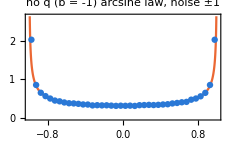
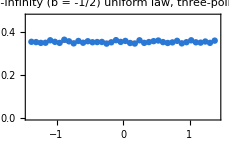
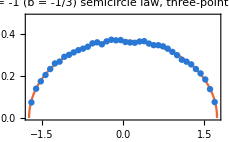
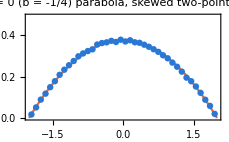
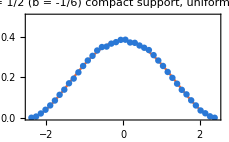
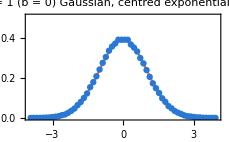
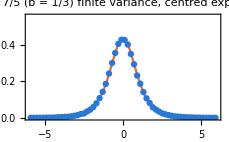
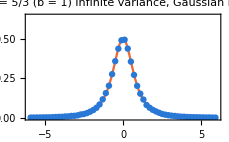
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
fig1 = Grid[Partition[fig1Panels, 5, 5, {1, 1}, {}]]
```

```mathematica
binDev[b_, kind_] := Module[{yN = sims[{b, kind}]["final"], lo, hi, nb = 20, edges, cnt, ex},
   {lo, hi} = range1[b]; edges = lo + (hi - lo) Range[0, nb]/nb; cnt = BinCounts[yN, {edges}]/N[Length[yN]];
   ex = Differences[cdfG[b, edges]]; Max[Abs[cnt - ex]/Sqrt[ex (1 - ex)/Length[yN] + 10^-12]]];
```

```mathematica
fig1Cases = {{-1, "rademacher"}, {-1/2, "three"}, {-1/3, "three"}, {-1/4, "two"}, {-1/6, "uniform"}, {0, "exp"}, {1/3, "exp"}, {1, "gauss"}, {2, "rademacher"}};
```

```mathematica
fig1Dev = Table[binDev[cs[[1]], cs[[2]]], {cs, fig1Cases}]
```

{2.10005,1.45689,2.5199,3.04489,2.36707,2.29921,2.75398,1.70862,1.62726}

```mathematica
check["Fig. 1: in each of the nine panels (a)-(i) the bin probabilities (20 bins) agree with those of g_b within six standard errors", Max[fig1Dev] < 6]
```

PASS   Fig. 1: in each of the nine panels (a)-(i) the bin probabilities (20 bins) agree with those of g_b within six standard errors

Figure 2: tail probability P(|S_N/Sqrt[N]| > x) at the largest N (points) and the exact tail of g_b (lines), b = 1/3, 1, 2

```mathematica
tailExact[b_, x_] := BetaRegularized[(1 + 1/b)/((1 + 1/b) + (1 + b) x^2), (1 + 1/b)/2, 1/2];
```

```mathematica
tailXs = 10.^Range[0, 2.5, 0.1];
```

```mathematica
tailEmp[b_, kind_] := With[{a = Abs[sims[{b, kind}]["final"]]}, Table[{x, N[Mean[UnitStep[a - x]]]}, {x, tailXs}]];
```

```mathematica
tailCases = {{1/3, "gauss"}, {1, "exp"}, {2, "rademacher"}};
```

```mathematica
tailData = tailEmp @@@ tailCases;
```

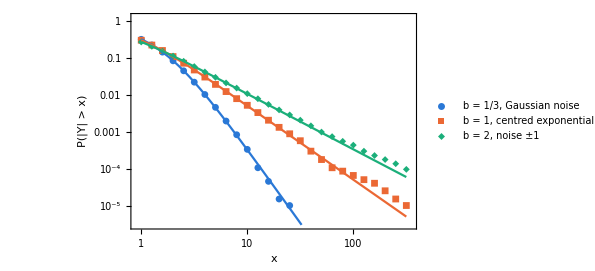

```mathematica
fig2 = Show[ListLogLogPlot[Select[#, #[[2]] > 0 &] & /@ tailData, PlotStyle -> {colB, colO, colA}, PlotMarkers -> {Automatic, 7}, PlotRange -> {{0.9, 350}, {3*^-6, 1.2}},
    PlotLegends -> Placed[{"b = 1/3, Gaussian noise", "b = 1, centred exponential noise", "b = 2, noise ±1"}, {0.3, 0.2}]],
   LogLogPlot[Evaluate[{tailExact[1/3, x], tailExact[1, x], tailExact[2, x]}], {x, 1, 316}, PlotStyle -> {colB, colO, colA}, PlotRange -> {{0.9, 350}, {3*^-6, 1.2}}],
   Frame -> True, Axes -> False, FrameLabel -> {"x", "P(|Y| > x)"}, ImageSize -> 440]
```

```mathematica
tailDev = Max[Flatten[MapThread[Function[{cs, dat}, (Abs[#[[2]] - tailExact[cs[[1]], #[[1]]]] - 0.03 tailExact[cs[[1]], #[[1]]])/Sqrt[tailExact[cs[[1]], #[[1]]]/mPaths] & /@ dat], {tailCases, tailData}]]]
```

2.42351

```mathematica
check["Fig. 2: the simulated tail probabilities agree with the exact tails, which decay like x^-(1+1/b), within five standard errors plus 3%", tailDev < 5]
```

PASS   Fig. 2: the simulated tail probabilities agree with the exact tails, which decay like x^-(1+1/b), within five standard errors plus 3%

```mathematica
check["Fig. 2: the exact tails have the exponents 4, 2 and 3/2 (local slope at x = 10^4)",
  And @@ MapThread[Abs[(Log[tailExact[#1, 2. 10^4]] - Log[tailExact[#1, 10.^4]])/Log[2.] + #2] < 0.01 &, {{1/3, 1, 2}, {4, 2, 3/2}}]]
```

PASS   Fig. 2: the exact tails have the exponents 4, 2 and 3/2 (local slope at x = 10^4)

Additional figure (displaced start): the starting value S_1 = 4 is forgotten at the rate N^(-1/2)

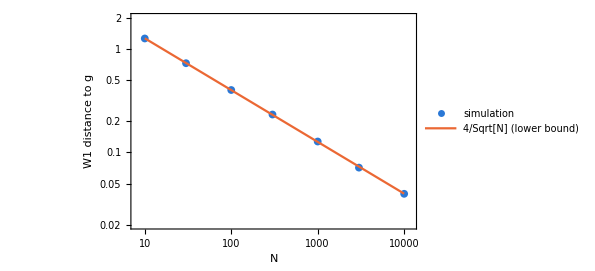

```mathematica
fig3 = Show[ListLogLogPlot[Transpose[{cps, simD["w1"]}], PlotStyle -> colB, PlotMarkers -> {Automatic, 8}, PlotRange -> {{8, 12000}, {0.02, 2}}, PlotLegends -> Placed[{"simulation"}, {0.75, 0.88}]],
   LogLogPlot[4/Sqrt[x], {x, 10, 10000}, PlotStyle -> colO, PlotRange -> {{8, 12000}, {0.02, 2}}, PlotLegends -> Placed[{"4/Sqrt[N] (lower bound)"}, {0.75, 0.78}]],
   Frame -> True, Axes -> False, FrameLabel -> {"N", "W1 distance to g"}, ImageSize -> 440]
```

## 8. Lemma 6: additional numerical check of the one-step defect (additional tables and figure)

Lemma 6 (additional numerical check): the one-step defect W1(g K^eps, g) by numerical integration, c = 1. half[b, x] = P(Y > |x|). The absolute difference of the two distribution functions is integrated with the trapezoidal rule after the substitution x = Sinh[u], on 20001 points of -45 <= u <= 45 (the method of the Python scripts). Survival functions are compared for x >= 0 and distribution functions for x < 0, which keeps the relative precision in both tails. The arithmetic is exact in b, eps and the noise values and uses 30 digits on the grid: at machine precision the incomplete Beta function is not accurate enough for the smallest values (about 10^-10), which spoiled the fitted powers for b = 1. The table takes about two minutes

```mathematica
half[b_, x_] := BetaRegularized[(1 + 1/b)/((1 + 1/b) + (1 + b) x^2), (1 + 1/b)/2, 1/2]/2;
```

```mathematica
upperG[b_, y_] := If[y >= 0, half[b, y], 1 - half[b, y]];
```

```mathematica
lowerG[b_, y_] := If[y < 0, half[b, y], 1 - half[b, y]];
```

```mathematica
tInv[b_, rho_, e_, x_] := (rho x - e Sqrt[b x^2 + rho^2 - e^2 b])/(rho^2 - e^2 b);
```

```mathematica
check["Lemma 6 (additional numerical check): the explicit inverse of Psi_i(y) = rho y + e sigma(y), c = 1",
  And @@ Flatten@Table[With[{rho = Sqrt[1 - ep^2], e = ep xi}, close[tInv[b, rho, e, rho y + e sig[y, b, 1]], y, 10^-10]], {b, {1/3, 1, 2}}, {ep, {1/5, 1/40}}, {xi, {2, -1/2, 1, -1}}, {y, {-30, -2, 0, 1/3, 7}}]]
```

PASS   Lemma 6 (additional numerical check): the explicit inverse of Psi_i(y) = rho y + e sigma(y), c = 1

```mathematica
defectIntegrand[b_, ep_, at_, x_?NumericQ] := With[{rho = Sqrt[1 - ep^2]},
   Abs[Sum[a[[2]] If[x >= 0, upperG[b, tInv[b, rho, ep a[[1]], x]], lowerG[b, tInv[b, rho, ep a[[1]], x]]], {a, at}] - half[b, x]]];
```

```mathematica
defect[b_, ep_, at_] := Module[{np = 20000, ug, xg, rho = Sqrt[1 - ep^2], st, mix, yy, hh, sy},
   ug = N[-45 + 90 Range[0, np]/np, 30]; xg = Sinh[ug]; st = UnitStep[xg]; mix = 0 xg;
   Do[yy = tInv[b, rho, ep a[[1]], xg]; hh = half[b, yy]; sy = UnitStep[yy];
    mix += a[[2]] (st (sy hh + (1 - sy) (1 - hh)) + (1 - st) ((1 - sy) hh + sy (1 - hh))), {a, at}];
   N[(90/np) Total[Abs[mix - half[b, xg]] Cosh[ug]]]];
```

```mathematica
defectNI[b_, ep_, at_] := Quiet@NIntegrate[defectIntegrand[b, ep, at, Sinh[u]] Cosh[u], {u, -45, 0, 45}, MaxRecursion -> 30, PrecisionGoal -> 5, Method -> "GlobalAdaptive"];
```

```mathematica
check["Lemma 6 (additional numerical check): the trapezoidal value of W1(g K^eps, g) agrees with adaptive integration (NIntegrate) within 1% (b = 1/3, skewed noise, eps = 1/10; b = 2, noise +1/-1, eps = 1/10)",
  Abs[defect[1/3, 1/10, atoms["two"]]/defectNI[1/3., 0.1, N[atoms["two"]]] - 1] < 0.01 && Abs[defect[2, 1/10, atoms["rademacher"]]/defectNI[2., 0.1, N[atoms["rademacher"]]] - 1] < 0.01]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1/2+1/2 (1-1/2 BetaRegularized[97/99,3/4,1/2])+1/4 BetaRegularized[97/99,3/4,1/2].

PASS   Lemma 6 (additional numerical check): the trapezoidal value of W1(g K^eps, g) agrees with adaptive integration (NIntegrate) within 1% (b = 1/3, skewed noise, eps = 1/10; b = 2, noise +1/-1, eps = 1/10)

```mathematica
epsList[b_, at_] := Select[{1/5, 1/10, 1/20, 1/40, 1/80, 1/160}, # Max[Abs[at[[All, 1]]]] Sqrt[b] <= 1/4 &];
```

```mathematica
defTab = Flatten[Table[With[{es = epsList[b, atoms[k]]}, <|"b" -> b, "noise" -> k, "eps" -> es, "w1" -> (defect[b, #, atoms[k]] & /@ es)|>], {b, {1/3, 1, 2}}, {k, {"two", "rademacher"}}], 1];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1/2+1/2 (1-1/2 BetaRegularized[71/72,2,1/2])+1/4 BetaRegularized[71/72,2,1/2].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1/2+1/2 (1-1/2 BetaRegularized[296/297,2,1/2])+1/4 BetaRegularized[296/297,2,1/2].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1/2+1/2 (1-1/2 BetaRegularized[1196/1197,2,1/2])+1/4 BetaRegularized[1196/1197,2,1/2].

General::stop: Further output of N::meprec will be suppressed during this calculation.

```mathematica
slopeOf[r_] := Fit[Log[N[Transpose[{r["eps"], r["w1"]}]]], {1, zfit}, zfit][[2, 1]];
```

Additional table (one-step defect): fitted power of eps, the ratio W1/eps^3 at the smallest eps, a_1 and C_L

```mathematica
table3 = Grid[Prepend[Table[{r["b"], r["noise"], N[m3[r["noise"]]], NumberForm[slopeOf[r], {4, 2}], Last[r["w1"]]/Last[r["eps"]]^3, N[a1Of[r["b"], 1]], N[clOf[r["b"], 1, m3[r["noise"]]]]}, {r, defTab}],
   {"b", "noise", "M3", "fitted power of eps", "W1/eps^3 at eps = 1/160", "a_1", "C_L"}], Frame -> All, Background -> {None, {1 -> LightGray}}]
```

b | noise | M3 | fitted power of eps | W1/eps^3 at eps = 1/160 | a_1 | C_L
1/3 | two | 1.7 | 3.01 | 0.162388 | 1.1781 | 129.846
1/3 | rademacher | 1. | 4.01 | 0.000844868 | 1.1781 | 76.38
1 | two | 1.7 | 4.01 | 0.00162772 | 1.5708 | 214.963
1 | rademacher | 1. | 4.01 | 0.00104171 | 1.5708 | 126.449
2 | two | 1.7 | 3.01 | 0.258955 | 2.18844 | 442.721
2 | rademacher | 1. | 4.01 | 0.00184439 | 2.18844 | 260.424

```mathematica
check["Lemma 6, (IV.6): W1(g K^eps, g) <= C_L eps^3 for every computed case", And @@ Flatten@Table[MapThread[#2 <= clOf[r["b"], 1, m3[r["noise"]]] #1^3 &, {r["eps"], r["w1"]}], {r, defTab}]]
```

PASS   Lemma 6, (IV.6): W1(g K^eps, g) <= C_L eps^3 for every computed case

```mathematica
check["Additional table (one-step defect): the fitted power of eps is 3.01 (b = 1/3 and b = 2, skewed noise) and 4.01 in the four other cases",
  And @@ MapThread[Abs[slopeOf[#1] - #2] < 0.03 &, {defTab, {3.01, 4.01, 4.01, 4.01, 3.01, 4.01}}]]
```

PASS   Additional table (one-step defect): the fitted power of eps is 3.01 (b = 1/3 and b = 2, skewed noise) and 4.01 in the four other cases

```mathematica
defRef = {{1/3, "two", 1/10, 1.643066*^-4}, {1/3, "two", 1/160, 3.964532*^-8}, {1/3, "rademacher", 1/10, 1.364467*^-5}, {1, "two", 1/10, 2.654080*^-5}, {1, "rademacher", 1/10, 1.686902*^-5}, {2, "two", 1/20, 3.278223*^-5}, {2, "two", 1/160, 6.322132*^-8}, {2, "rademacher", 1/10, 2.998854*^-5}};
```

```mathematica
check["Additional table (one-step defect) and Additional figure (one-step defect): the values of W1(g K^eps, g) agree with those obtained with the Python scripts of the manuscript within 1%",
  And @@ Table[With[{r = SelectFirst[defTab, #["b"] == ref[[1]] && #["noise"] == ref[[2]] &]}, Abs[r["w1"][[Position[r["eps"], ref[[3]]][[1, 1]]]]/ref[[4]] - 1] < 0.01], {ref, defRef}]]
```

PASS   Additional table (one-step defect) and Additional figure (one-step defect): the values of W1(g K^eps, g) agree with those obtained with the Python scripts of the manuscript within 1%

The explanation of the powers: the term of order eps^3 is (E xi^3/6) Int h''' sigma^3 g. Taking the supremum over h gives the prediction W1/eps^3 -> (|E xi^3|/6) Int |(sigma^3 g)''| dy

```mathematica
thirdCoef[b_] := NIntegrate[Evaluate[Abs[D[(1 + b y^2)^(3/2 - kap[b])/zz[b, 1], {y, 2}]]], {y, -Infinity, Infinity}, MaxRecursion -> 30]/6;
```

```mathematica
check["Lemma 6 (additional numerical check): sigma^3 g is constant for b = 1 (kappa = 3/2), so the term of order eps^3 vanishes for every noise", kap[1] == 3/2 && Simplify[D[(c + y^2)^(3/2) (c + y^2)^(-kap[1]), y]] === 0]
```

PASS   Lemma 6 (additional numerical check): sigma^3 g is constant for b = 1 (kappa = 3/2), so the term of order eps^3 vanishes for every noise

```mathematica
check["Lemma 6 (additional numerical check): for the skewed two-point noise E xi^3 = 3/2; for the noise +1/-1 E xi^3 = 0", Total[#[[1]]^3 #[[2]] & /@ atoms["two"]] == 3/2 && Total[#[[1]]^3 #[[2]] & /@ atoms["rademacher"]] == 0]
```

PASS   Lemma 6 (additional numerical check): for the skewed two-point noise E xi^3 = 3/2; for the noise +1/-1 E xi^3 = 0

```mathematica
thirdPred = {3/2 Quiet@thirdCoef[1/3], 3/2 Quiet@thirdCoef[2]}
```

{0.16238,0.258903}

```mathematica
check["Lemma 6 (additional numerical check): for the skewed noise the measured W1/eps^3 at eps = 1/160 equals the predicted limit (E xi^3/6) Int |(sigma^3 g)''| = 0.1624 (b = 1/3) and 0.2589 (b = 2) within 1%",
  close[thirdPred[[1]], 0.16238, 10^-3] && close[thirdPred[[2]], 0.25890, 10^-3] &&
   Abs[Last[defTab[[1]]["w1"]]/Last[defTab[[1]]["eps"]]^3/thirdPred[[1]] - 1] < 0.01 && Abs[Last[defTab[[5]]["w1"]]/Last[defTab[[5]]["eps"]]^3/thirdPred[[2]] - 1] < 0.01]
```

PASS   Lemma 6 (additional numerical check): for the skewed noise the measured W1/eps^3 at eps = 1/160 equals the predicted limit (E xi^3/6) Int |(sigma^3 g)''| = 0.1624 (b = 1/3) and 0.2589 (b = 2) within 1%

Additional figure (one-step defect): one-step defect against eps, skewed two-point noise

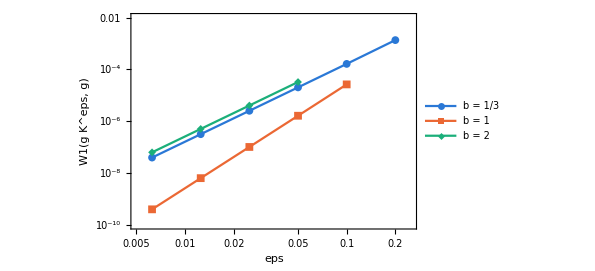

```mathematica
fig4 = ListLogLogPlot[Table[Transpose[{r["eps"], r["w1"]}], {r, defTab[[{1, 3, 5}]]}], Joined -> True, PlotMarkers -> {Automatic, 8}, PlotStyle -> {colB, colO, colA}, PlotRange -> {{0.005, 0.25}, {10^-10, 10^-2}},
   PlotLegends -> Placed[{"b = 1/3", "b = 1", "b = 2"}, {0.25, 0.8}], Frame -> True, Axes -> False, FrameLabel -> {"eps", "W1(g K^eps, g)"}, ImageSize -> 440]
```

Additional table (constants of Theorem B): the constants of Theorem B

```mathematica
table4 = Grid[Prepend[Table[{r["b"], r["noise"], N[m3[r["noise"]]], ScientificForm[N[lamOf[r["b"], m3[r["noise"]]]], 3], NumberForm[N[clOf[r["b"], 1, m3[r["noise"]]]], {5, 1}]}, {r, defTab}], {"b", "noise", "M3", "Lambda (IV.4)", "C_L (IV.7)"}], Frame -> All, Background -> {None, {1 -> LightGray}}]
```

b | noise | M3 | Lambda (IV.4) | C_L (IV.7)
1/3 | two | 1.7 | 1.98×10^1 | 129.8
1/3 | rademacher | 1. | 5.79 | 76.4
1 | two | 1.7 | 5.42×10^6 | 215.0
1 | rademacher | 1. | 9.15×10^3 | 126.4
2 | two | 1.7 | 1.11×10^19 | 442.7
2 | rademacher | 1. | 1.6×10^11 | 260.4

## 9. Corollary D: the Cauchy law, q = 2 (Sec. V B, Appendix C 3, Table III, Figure 3)

The four facts and the final step of the proof of Corollary D, the two remarks after it, the simulation of Appendix C 3 (six runs with the parameters of Section 6, about half the time of Section 6), and panel (j) of Figure 1 (q = 2).

Cor. D, proof, first fact: with c_b = c (1 + b), the limit law g_b is Student's law with nu = 1 + 1/b degrees of freedom and scale Sqrt[c], for every b

```mathematica
check["Cor. D, proof, first fact: with c_b = c(1+b), g_b is the law of Sqrt[c] T_nu, nu = 1 + 1/b (b = 1, 5, 50; c = 1, 23/10)",
  And @@ Flatten@Table[close[gb[y, b, c (1 + b)], PDF[StudentTDistribution[0, Sqrt[c], 1 + 1/b], y], 10^-10], {b, {1, 5, 50}}, {c, {1, 23/10}}, {y, {-7/2, 0, 1/3, 5}}]]
```

PASS   Cor. D, proof, first fact: with c_b = c(1+b), g_b is the law of Sqrt[c] T_nu, nu = 1 + 1/b (b = 1, 5, 50; c = 1, 23/10)

Cor. D, proof, second fact: the Student density at nu = 1 is the Cauchy density, and the L1 distance of the densities tends to 0 as b -> Infinity

```mathematica
check["Cor. D, proof, second fact: the Student density with nu = 1 is the Cauchy density 1/(Pi(1+t^2))", FullSimplify[PDF[StudentTDistribution[1], t] - 1/(Pi (1 + t^2))] === 0]
```

PASS   Cor. D, proof, second fact: the Student density with nu = 1 is the Cauchy density 1/(Pi(1+t^2))

```mathematica
l1Dist[b_] := 2 NIntegrate[Abs[PDF[StudentTDistribution[1 + 1/b], t] - 1/(Pi (1 + t^2))], {t, 0, 1, 10, 100, 10^4, Infinity}, MaxRecursion -> 50, PrecisionGoal -> 6];
```

```mathematica
l1Tab = Table[{b, Quiet@l1Dist[N[b]]}, {b, {5, 20, 50, 200, 1000}}]
```

{{5,0.0696927},{20,0.0193775},{50,0.00792852},{200,0.00200507},{1000,0.000402256}}

```mathematica
check["Cor. D, proof, second fact: the L1 distance between f_nu and f_1 decreases in b and is below 0.41/b (b = 5, 20, 50, 200, 1000)",
  And @@ (Greater @@@ Partition[l1Tab[[All, 2]], 2, 1]) && And @@ (#[[1]] #[[2]] < 0.41 & /@ l1Tab)]
```

PASS   Cor. D, proof, second fact: the L1 distance between f_nu and f_1 decreases in b and is below 0.41/b (b = 5, 20, 50, 200, 1000)

Exact Kolmogorov distance between g_b (scale 1) and the standard Cauchy law, by maximizing over a fine logarithmic grid

```mathematica
tCDF[nu_, y_] := 0.5 + Sign[y] (1 - BetaRegularized[nu/(nu + y^2), nu/2, 0.5])/2;
```

```mathematica
cauchyCDF[y_] := 0.5 + ArcTan[y]/Pi;
```

```mathematica
ksExact[b_] := With[{ts = 10.^Range[-4., 7., 0.0005]}, Max[Abs[tCDF[1. + 1/b, ts] - cauchyCDF[ts]]]];
```

```mathematica
check["App. C 3: the exact Kolmogorov distance between g_b and the Cauchy law is 0.01742, 0.00484, 0.00198 for b = 5, 20, 50, and about 0.1/b for large b",
  Abs[ksExact[5] - 0.017423] < 2 10^-5 && Abs[ksExact[20] - 0.004844] < 2 10^-5 && Abs[ksExact[50] - 0.001982] < 2 10^-5 && Abs[1000 ksExact[1000] - 0.1006] < 0.002]
```

PASS   App. C 3: the exact Kolmogorov distance between g_b and the Cauchy law is 0.01742, 0.00484, 0.00198 for b = 5, 20, 50, and about 0.1/b for large b

Cor. D, proof, (a): the Beta integral (V.3) and the bound on a_1

```mathematica
check["(V.3): Int (c + b y^2)^(-s) dy = c^(1/2-s) Sqrt[Pi/b] Gamma[s-1/2]/Gamma[s] (numerical; s = 3/4, 1, 3/2, 3; b = 1/2, 2, 50; c = 1, 23/5)",
  And @@ Flatten@Table[close[Quiet@NIntegrate[(c + b y^2)^(-s), {y, -Infinity, Infinity}, MaxRecursion -> 50], c^(1/2 - s) Sqrt[Pi/b] Gamma[s - 1/2]/Gamma[s], 10^-5], {s, {3/4, 1, 3/2, 3}}, {b, {1/2, 2, 50}}, {c, {1, 23/5}}]]
```

PASS   (V.3): Int (c + b y^2)^(-s) dy = c^(1/2-s) Sqrt[Pi/b] Gamma[s-1/2]/Gamma[s] (numerical; s = 3/4, 1, 3/2, 3; b = 1/2, 2, 50; c = 1, 23/5)

```mathematica
check["Cor. D, proof, (a): (V.3) with s = kappa - 1/2 divided by (V.3) with s = kappa gives a_1 = Sqrt[c] Gamma[kappa-1] Gamma[kappa]/Gamma[kappa-1/2]^2",
  FullSimplify[(c^(1/2 - (k - 1/2)) Sqrt[Pi/b] Gamma[k - 1]/Gamma[k - 1/2])/(c^(1/2 - k) Sqrt[Pi/b] Gamma[k - 1/2]/Gamma[k]) == Sqrt[c] Gamma[k - 1] Gamma[k]/Gamma[k - 1/2]^2, {c > 0, b > 0, k > 1}]]
```

PASS   Cor. D, proof, (a): (V.3) with s = kappa - 1/2 divided by (V.3) with s = kappa gives a_1 = Sqrt[c] Gamma[kappa-1] Gamma[kappa]/Gamma[kappa-1/2]^2

```mathematica
check["Cor. D, proof, (a): Gamma[x] <= 1/x and Gamma[1+x] <= 1 for 0 < x <= 1; Gamma[1/2+x] >= 1 for 0 < x <= 1/2",
  And @@ Table[N[Gamma[x]] <= N[1/x] + 10^-12 && N[Gamma[1 + x]] <= 1 + 10^-12, {x, 1/1000, 1, 1/1000}] && And @@ Table[N[Gamma[1/2 + x]] >= 1 - 10^-12, {x, 1/1000, 1/2, 1/1000}]]
```

PASS   Cor. D, proof, (a): Gamma[x] <= 1/x and Gamma[1+x] <= 1 for 0 < x <= 1; Gamma[1/2+x] >= 1 for 0 < x <= 1/2

```mathematica
check["Cor. D, proof, (a): a_1 <= 2 b Sqrt[c_b] for b >= 1 (a_1 is proportional to Sqrt[c], so c_b = 1 suffices; b = 1..10^5)",
  And @@ Table[N[a1Of[b, 1]] <= N[2 b] + 10^-12, {b, 10^Range[0, 5, 1/20]}]]
```

PASS   Cor. D, proof, (a): a_1 <= 2 b Sqrt[c_b] for b >= 1 (a_1 is proportional to Sqrt[c], so c_b = 1 suffices; b = 1..10^5)

```mathematica
check["Cor. D, proof, (b): C_L <= 161 M3 b^2 Sqrt[c_b] for b >= 1 (b = 1..10^5; M3 = 1, 17/10, 5)",
  And @@ Flatten@Table[N[clOf[b, 1 + b, m]] <= N[161 m b^2 Sqrt[1 + b]], {b, 10^Range[0, 5, 1/20]}, {m, {1, 17/10, 5}}]]
```

PASS   Cor. D, proof, (b): C_L <= 161 M3 b^2 Sqrt[c_b] for b >= 1 (b = 1..10^5; M3 = 1, 17/10, 5)

Cor. D, proof, (c): E|Y_3| computed exactly by enumerating all noise values of the first three steps

```mathematica
eY3[b_, cb_, at_] := Total[Function[p, Module[{y = Sqrt[cb] p[[1, 1]]}, Do[y = Sqrt[n/(n + 1)] y + 1/Sqrt[n + 1] Sqrt[cb + b y^2] p[[n + 1, 1]], {n, 1, 2}]; Abs[y] Times @@ p[[All, 2]]]] /@ Tuples[at, 3]];
```

```mathematica
check["Cor. D, proof, (c): E|Y_3| <= (3 + 3 Sqrt[b] + b) Sqrt[c_b], exact for noise +1/-1, three-point and skewed two-point (b = 1, 2, 5, 50, 1000; c = 1, 23/10)",
  And @@ Flatten@Table[N[eY3[b, c (1 + b), atoms[k]]] <= N[(3 + 3 Sqrt[b] + b) Sqrt[c (1 + b)]], {k, {"rademacher", "three", "two"}}, {b, {1, 2, 5, 50, 1000}}, {c, {1, 23/10}}]]
```

PASS   Cor. D, proof, (c): E|Y_3| <= (3 + 3 Sqrt[b] + b) Sqrt[c_b], exact for noise +1/-1, three-point and skewed two-point (b = 1, 2, 5, 50, 1000; c = 1, 23/10)

```mathematica
eAbsG[b_, c_] := Sqrt[c] 2 Sqrt[1 + 1/b] Gamma[(2 + 1/b)/2]/(Sqrt[Pi] (1/b) Gamma[(1 + 1/b)/2]);
```

```mathematica
check["Cor. D, proof, (c): E_g|Y| = 2 Sqrt[c nu] Gamma((nu+1)/2)/(Sqrt[Pi] (nu-1) Gamma(nu/2)) for the law Sqrt[c] T_nu (numerical check, b = 1, 3, 5)",
  And @@ Table[close[eAbsG[b, 1], Quiet@NIntegrate[2 y PDF[StudentTDistribution[1 + 1/b], y], {y, 0, 1, 100, Infinity}, MaxRecursion -> 50], 10^-4], {b, {1, 3, 5}}]]
```

PASS   Cor. D, proof, (c): E_g|Y| = 2 Sqrt[c nu] Gamma((nu+1)/2)/(Sqrt[Pi] (nu-1) Gamma(nu/2)) for the law Sqrt[c] T_nu (numerical check, b = 1, 3, 5)

```mathematica
check["Cor. D, proof, (c): E_g|Y| <= a_1/Sqrt[b] <= 2 Sqrt[b] Sqrt[c_b] (b = 1..10^4, c = 1)",
  And @@ Table[N[eAbsG[b, 1]] <= N[a1Of[b, 1 + b]/Sqrt[b]] (1 + 10^-12) && N[a1Of[b, 1 + b]/Sqrt[b]] <= N[2 Sqrt[b] Sqrt[1 + b]], {b, 10^Range[0, 4, 1/20]}]]
```

PASS   Cor. D, proof, (c): E_g|Y| <= a_1/Sqrt[b] <= 2 Sqrt[b] Sqrt[c_b] (b = 1..10^4, c = 1)

```mathematica
check["Cor. D, proof, (c): 3 + 5 Sqrt[b] + b <= 9 b for b >= 1 (with u = Sqrt[b])", Resolve[ForAll[u, u >= 1, 3 + 5 u + u^2 <= 9 u^2], Reals]]
```

PASS   Cor. D, proof, (c): 3 + 5 Sqrt[b] + b <= 9 b for b >= 1 (with u = Sqrt[b])

Cor. D, proof, (d): the bound (V.4). Lambda multiplies both sides and is left out

```mathematica
check["(V.4): Sqrt[3/N] 9 b Sqrt[c_b] + 161 M3 b^2 Sqrt[c_b] ln(N/3)/Sqrt[N] <= 251 M3 Sqrt[c] b^(5/2) (1 + ln N)/Sqrt[N] (c = 1; b = 1..10^4; N = 3..10^12; M3 = 1, 17/10, 5)",
  And @@ Flatten@Table[Sqrt[3./nn] 9 b Sqrt[1. + b] + 161 m b^2 Sqrt[1. + b] Log[nn/3.]/Sqrt[nn] <= 251 m b^2.5 (1 + Log[nn])/Sqrt[nn], {b, 10.^Range[0, 4, 0.1]}, {nn, Join[{3., 4., 10.}, 10.^Range[2, 12, 0.5]]}, {m, {1, 1.7, 5}}]]
```

PASS   (V.4): Sqrt[3/N] 9 b Sqrt[c_b] + 161 M3 b^2 Sqrt[c_b] ln(N/3)/Sqrt[N] <= 251 M3 Sqrt[c] b^(5/2) (1 + ln N)/Sqrt[N] (c = 1; b = 1..10^4; N = 3..10^12; M3 = 1, 17/10, 5)

Cor. D, proof, final step

```mathematica
check["Cor. D, proof, final step: Sum over j >= 2 of j^(-3/2) equals Zeta(3/2) - 1", Sum[j^(-3/2), {j, 2, Infinity}] == Zeta[3/2] - 1]
```

PASS   Cor. D, proof, final step: Sum over j >= 2 of j^(-3/2) equals Zeta(3/2) - 1

```mathematica
check["(II.6): theta_* = 1/(8 Sqrt[2] (Zeta(3/2) - 1) M3) = 0.054819/M3, and chi = 4 Sqrt[2] (Zeta(3/2) - 1) M3 theta = theta/(2 theta_*)",
  close[1/(8 Sqrt[2] (Zeta[3/2] - 1)), 0.0548187, 10^-5] && Simplify[4 Sqrt[2] (z - 1) m th == th/(2/(8 Sqrt[2] (z - 1) m))]]
```

PASS   (II.6): theta_* = 1/(8 Sqrt[2] (Zeta(3/2) - 1) M3) = 0.054819/M3, and chi = 4 Sqrt[2] (Zeta(3/2) - 1) M3 theta = theta/(2 theta_*)

```mathematica
check["Cor. D, proof, final step: if b^(3/2) = theta ln N, then Lambda = N^chi (theta = 1/100, 1/30; M3 = 1, 17/10; N = 10, 10^5, 10^12)",
  And @@ Flatten@Table[close[lamOf[(th Log[nn])^(2/3), m], nn^(4 Sqrt[2] (Zeta[3/2] - 1) m th), 10^-10], {th, {1/100, 1/30}}, {m, {1, 17/10}}, {nn, {10, 10^5, 10^12}}]]
```

PASS   Cor. D, proof, final step: if b^(3/2) = theta ln N, then Lambda = N^chi (theta = 1/100, 1/30; M3 = 1, 17/10; N = 10, 10^5, 10^12)

```mathematica
check["Cor. D, proof, final step: (theta ln N)^(5/3) (1 + ln N) N^(chi - 1/2) -> 0 when chi < 1/2 (theta = 1/20, chi = 49/100)",
  Limit[(Log[nn]/20)^(5/3) (1 + Log[nn]) nn^(49/100 - 1/2), nn -> Infinity] == 0]
```

PASS   Cor. D, proof, final step: (theta ln N)^(5/3) (1 + ln N) N^(chi - 1/2) -> 0 when chi < 1/2 (theta = 1/20, chi = 49/100)

```mathematica
check["Corollary D: q_N = (1 + 4 b_N)/(1 + 2 b_N) -> 2 as b_N -> Infinity", Limit[qOf[b], b -> Infinity] == 2]
```

PASS   Corollary D: q_N = (1 + 4 b_N)/(1 + 2 b_N) -> 2 as b_N -> Infinity

```mathematica
check["Remark (an equivalent form): (1 + b)(c + b u^2/n) = c(1 + b) + b (Sqrt[1+b] u)^2/n, so Sqrt[1+b] U_n follows the recursion with c_N = c(1+b)",
  Simplify[(1 + b) (c + b u^2/n) == c (1 + b) + b (Sqrt[1 + b] u)^2/n]]
```

PASS   Remark (an equivalent form): (1 + b)(c + b u^2/n) = c(1 + b) + b (Sqrt[1+b] u)^2/n, so Sqrt[1+b] U_n follows the recursion with c_N = c(1+b)

```mathematica
check["Remark (the growth condition): with M3 = 1 and theta = theta_*, b_N = (theta_* ln N)^(2/3) is about 1.17 at N = 10^10",
  Abs[(Log[10.^10]/(8 Sqrt[2] (Zeta[3/2] - 1)))^(2/3) - 1.168] < 0.001]
```

PASS   Remark (the growth condition): with M3 = 1 and theta = theta_*, b_N = (theta_* ln N)^(2/3) is about 1.17 at N = 10^10

App. C 3: simulation with c_b = 1 + b for b = 5, 20, 50. By Cor. D, proof, first fact the limit g_b is Student's law with 1 + 1/b degrees of freedom and scale 1; the Cauchy law has scale 1

```mathematica
ksF[y_, cdf_] := With[{f = cdf[Sort[y]], m = Length[y]}, Max[Max[Range[m]/N[m] - f], Max[f - (Range[m] - 1)/N[m]]]];
```

```mathematica
simQ2[b_, kind_] := Module[{s = Sqrt[1. + b] noise[kind, mPaths], bb = N[b], ks = {}, y},
   Do[s = s + Sqrt[(1. + bb) + bb s^2/n] noise[kind, mPaths];
    If[MemberQ[{100, 1000, nMax}, n + 1], y = s/Sqrt[n + 1.]; AppendTo[ks, ksF[y, tCDF[1. + 1/bb, #] &]]], {n, 1, nMax - 1}];
   y = s/Sqrt[N[nMax]];
   <|"b" -> b, "noise" -> kind, "ksG" -> ks, "ksC" -> ksF[y, cauchyCDF], "exact" -> ksExact[b], "maxS" -> Max[Abs[s]], "finite" -> VectorQ[s, NumericQ], "final" -> y|>];
```

```mathematica
q2cases = {{5, "gauss"}, {5, "rademacher"}, {20, "gauss"}, {20, "rademacher"}, {50, "gauss"}, {50, "rademacher"}};
```

```mathematica
q2Time = First@AbsoluteTiming[q2 = simQ2 @@@ q2cases;]
```

165.902

Table III

```mathematica
table5 = Grid[Prepend[Table[Join[{r["b"], r["noise"]}, NumberForm[#, {5, 4}] & /@ r["ksG"], {NumberForm[r["ksC"], {5, 4}], NumberForm[r["exact"], {5, 4}], ScientificForm[r["maxS"], 2]}], {r, q2}],
   {"b", "noise", "to g_b: N = 100", "1000", "largest N", "to Cauchy: largest N", "exact", "max |S_N|"}], Frame -> All, Background -> {None, {1 -> LightGray}}]
```

b | noise | to g_b: N = 100 | 1000 | largest N | to Cauchy: largest N | exact | max |S_N|
5 | gauss | 0.0058 | 0.0019 | 0.0021 | 0.0191 | 0.0174 | 3.3×10^6
5 | rademacher | 0.0019 | 0.0011 | 0.0017 | 0.0184 | 0.0174 | 1.3×10^7
20 | gauss | 0.0194 | 0.0029 | 0.0029 | 0.0055 | 0.0048 | 3.1×10^6
20 | rademacher | 0.0035 | 0.0010 | 0.0024 | 0.0054 | 0.0048 | 5.4×10^6
50 | gauss | 0.1070 | 0.0015 | 0.0030 | 0.0042 | 0.0020 | 3.5×10^6
50 | rademacher | 0.0015 | 0.0014 | 0.0016 | 0.0026 | 0.0020 | 5.7×10^6

```mathematica
check["Table III: all paths stay finite", And @@ (#["finite"] & /@ q2)]
```

PASS   Table III: all paths stay finite

```mathematica
check["Table III: at the largest N the distance to g_b is at the sampling level (below 1.95/Sqrt[M] + 0.002) in all six runs", And @@ (Last[#["ksG"]] < 1.95/Sqrt[mPaths] + 0.002 & /@ q2)]
```

PASS   Table III: at the largest N the distance to g_b is at the sampling level (below 1.95/Sqrt[M] + 0.002) in all six runs

```mathematica
check["Table III: the distance to the Cauchy law equals the exact distance between g_b and the Cauchy law within 1.95/Sqrt[M] + 0.002", And @@ (Abs[#["ksC"] - #["exact"]] < 1.95/Sqrt[mPaths] + 0.002 & /@ q2)]
```

PASS   Table III: the distance to the Cauchy law equals the exact distance between g_b and the Cauchy law within 1.95/Sqrt[M] + 0.002

Figure 3: exact distance between g_b and the Cauchy law (line), measured distance of S_N/Sqrt[N] to the Cauchy law (points), sampling level 0.8687/Sqrt[M] (dashed)

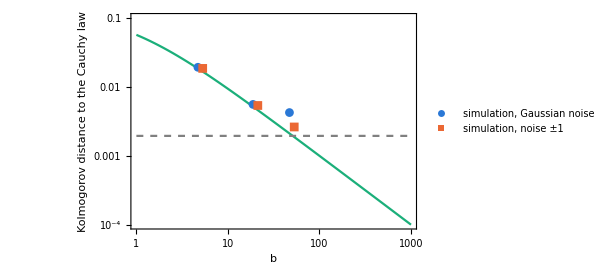

```mathematica
fig5 = Show[ListLogLogPlot[Table[{b, ksExact[b]}, {b, 10.^Range[0, 3, 0.05]}], Joined -> True, PlotStyle -> colA, PlotRange -> {{1, 1000}, {10^-4, 0.1}}],
   ListLogLogPlot[{Table[{0.94 r["b"], r["ksC"]}, {r, Select[q2, #["noise"] == "gauss" &]}], Table[{1.06 r["b"], r["ksC"]}, {r, Select[q2, #["noise"] == "rademacher" &]}]},
    PlotStyle -> {colB, colO}, PlotMarkers -> {Automatic, 9}, PlotLegends -> Placed[{"simulation, Gaussian noise", "simulation, noise ±1"}, {0.7, 0.85}]],
   LogLogPlot[0.8687/Sqrt[mPaths], {x, 1, 1000}, PlotStyle -> Directive[Gray, Dashed]],
   Frame -> True, Axes -> False, FrameLabel -> {"b", "Kolmogorov distance to the Cauchy law"}, ImageSize -> 440]
```

Figure 1, last panel (j), q = 2: histogram of S_N/Sqrt[N] at the largest N for b = 50, c_b = 1 + b, noise +1/-1 (points), and the Cauchy density 1/(Pi(1+y^2)) (line)

```mathematica
yQ2 = SelectFirst[q2, #["b"] == 50 && #["noise"] == "rademacher" &]["final"];
```

```mathematica
panelQ2 = Module[{edges = -6. + 12. Range[0, 60]/60, cnt, mid, hts, ymax},
   cnt = BinCounts[yQ2, {edges}]; mid = (Most[edges] + Rest[edges])/2; hts = cnt/(Length[yQ2] 0.2); ymax = 1.12 Max[hts];
   Show[Plot[1/(Pi (1 + y^2)), {y, -6, 6}, PlotStyle -> Directive[colO, Thickness[0.007]], PlotRange -> {{-6, 6}, {0, ymax}}, PlotPoints -> 200],
    ListPlot[Transpose[{mid, hts}], PlotStyle -> Directive[colB, PointSize[0.02]]],
    Frame -> True, Axes -> False, PlotRange -> {{-6, 6}, {0, ymax}}, PlotLabel -> Style["q = 2 (Corollary D, b = 50)\nCauchy law, noise ±1", 10],
    FrameLabel -> {"y", None}, ImageSize -> 230]];
```

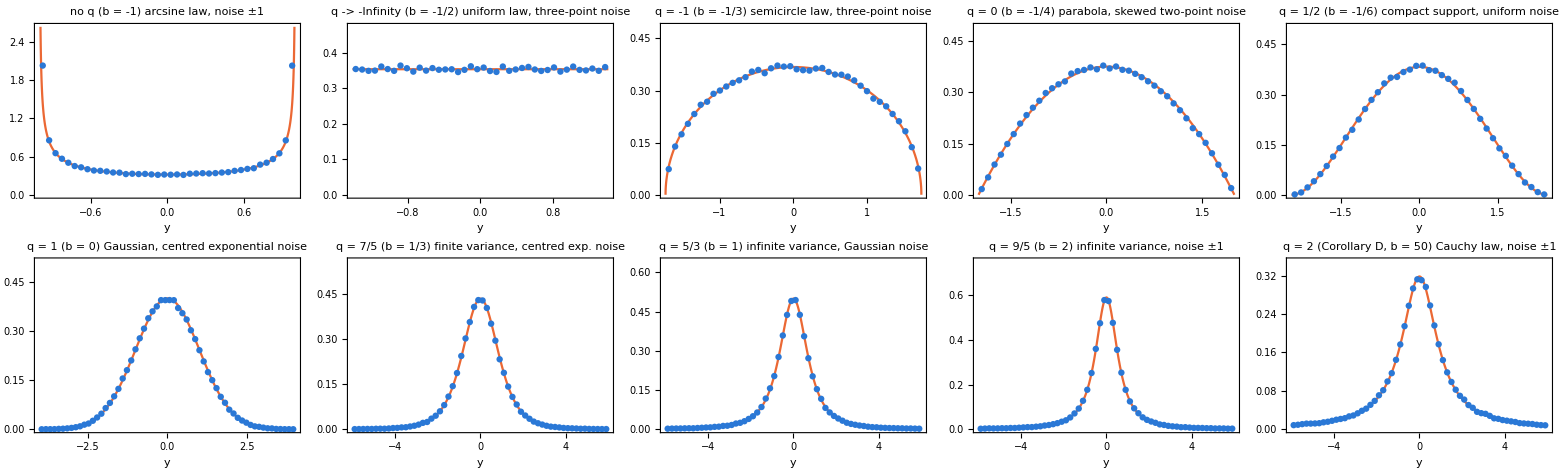

```mathematica
fig1Q2 = Grid[Partition[Append[fig1Panels, panelQ2], 5]]
```

```mathematica
binDevQ2 = Module[{edges = -6. + 12. Range[0, 20]/20, cnt, ex}, cnt = BinCounts[yQ2, {edges}]/N[Length[yQ2]];
   ex = Differences[tCDF[1. + 1/50, edges]]; Max[Abs[cnt - ex]/Sqrt[ex (1 - ex)/Length[yQ2]]]];
```

```mathematica
check["Figure 1, last panel: the bin probabilities (20 bins in [-6, 6]) agree with those of g_50 within six standard errors", binDevQ2 < 6]
```

PASS   Figure 1, last panel: the bin probabilities (20 bins in [-6, 6]) agree with those of g_50 within six standard errors

```mathematica
check["Figure 1, last panel: the mass outside |y| <= 6 agrees with that of g_50 (0.1018) within five standard errors; for the Cauchy law it is 0.1051",
  Abs[Mean[UnitStep[Abs[yQ2] - 6.]] - 2 (1 - tCDF[1. + 1/50, 6.])] < 5 Sqrt[0.102 0.898/Length[yQ2]] && Abs[2 (1 - cauchyCDF[6.]) - 0.10514] < 10^-4]
```

PASS   Figure 1, last panel: the mass outside |y| <= 6 agrees with that of g_50 (0.1018) within five standard errors; for the Cauchy law it is 0.1051

## 10. Appendix B: Proposition E (quadratic feedback characterizes the q-Gaussians)

Part (i): the formula (B.2) for D, for a generic density and for every g_b, and a non-quadratic example. Part (ii): with D = c + b y^2 the solution of (B.1) is g_b, on I_b. Part (iii): the q-Gaussians with q < 2 give D = c + b y^2 with b > -1/2, and those with 2 <= q < 3, among them the Cauchy law, have no first moment. All checks are exact or by numerical integration and take well under a minute.

Part (i): formula (B.2). For any density g, D = (1/g) Int_y^l t g dt satisfies (B.1); here gg is a generic function

```mathematica
check["Prop. E (i): D = (1/g) Int_y^l t g(t) dt satisfies (D g)' = -y g for a generic function g",
  Simplify[D[Integrate[t gg[t], {t, y, l}], y] + y gg[y]] === 0]
```

PASS   Prop. E (i): D = (1/g) Int_y^l t g(t) dt satisfies (D g)' = -y g for a generic function g

(B.2) applied to the limit laws g_b recovers D = c + b y^2. tailTG[b, c, y0] is Int_y0^l t g_b(t) dt, exact for b < 0 and numerical for b > 0

```mathematica
tailTG[b_, c_, y0_] := If[b > 0, NIntegrate[t (c + b t^2)^(-kap[b]), {t, y0, Infinity}, WorkingPrecision -> 30, PrecisionGoal -> 12],
    Integrate[t (c + b t^2)^(-kap[b]), {t, y0, Sqrt[-c/b]}]]/zz[b, c];
```

```mathematica
check["Prop. E (i): (B.2) applied to g_b gives D = c + b y^2 (b = 1/3, 1, 2, -1/4, -1/2, -1; c = 1, 23/10; y = 0, 1/2, 3, 20 for b > 0 and y = 0, L/3, 2L/3 for b < 0)",
  And @@ Flatten@Table[close[tailTG[b, c, y]/gb[y, b, c], c + b y^2, 10^-8],
     {b, {1/3, 1, 2, -1/4, -1/2, -1}}, {c, {1, 23/10}},
     {y, If[b > 0, {0, 1/2, 3, 20}, {0, 1/3, 2/3} Sqrt[-c/b]]}]]
```

PASS   Prop. E (i): (B.2) applied to g_b gives D = c + b y^2 (b = 1/3, 1, 2, -1/4, -1/2, -1; c = 1, 23/10; y = 0, 1/2, 3, 20 for b > 0 and y = 0, L/3, 2L/3 for b < 0)

```mathematica
check["Prop. E (i): g_b is even, so Int y g_b = 0, and Int |y| g_b = 2 Q(0) = 2 c g_b(0) (same values of b and c)",
  And @@ Flatten@Table[
     (And @@ Table[gb[-y0, b, c] == gb[y0, b, c], {y0, {1/5, 1/2, 9/10} If[b > 0, 10, Sqrt[-c/b]]}]) &&
      close[2 tailTG[b, c, 0], 2 c gb[0, b, c], 10^-8],
     {b, {1/3, 1, 2, -1/4, -1/2, -1}}, {c, {1, 23/10}}]]
```

PASS   Prop. E (i): g_b is even, so Int y g_b = 0, and Int |y| g_b = 2 Q(0) = 2 c g_b(0) (same values of b and c)

A non-quadratic example: for g proportional to Exp[-y^4], (B.2) gives the variance function D below. It satisfies (B.1) but is not of the form c + b y^2; it even decreases with |y|

```mathematica
dQuartic[y_] := Sqrt[Pi]/4 Exp[y^4] Erfc[y^2];
```

```mathematica
check["Prop. E (i), example: for g proportional to Exp[-y^4], (B.2) gives D = (Sqrt[Pi]/4) Exp[y^4] Erfc[y^2] (numerical, y = -3/2..2), which satisfies (B.1) and is not of the form c + b y^2",
  And @@ Table[close[NIntegrate[t Exp[-t^4], {t, y0, Infinity}, WorkingPrecision -> 30] Exp[y0^4], dQuartic[y0], 10^-10], {y0, {-3/2, -1/2, 0, 1/2, 1, 2}}] &&
   Simplify[D[dQuartic[y] Exp[-y^4], y] + y Exp[-y^4]] === 0 &&
   Abs[N[(dQuartic[2] - dQuartic[0])/(dQuartic[1] - dQuartic[0]) - 4]] > 1 && N[dQuartic[2]] < N[dQuartic[1]] < N[dQuartic[0]]]
```

PASS   Prop. E (i), example: for g proportional to Exp[-y^4], (B.2) gives D = (Sqrt[Pi]/4) Exp[y^4] Erfc[y^2] (numerical, y = -3/2..2), which satisfies (B.1) and is not of the form c + b y^2

Part (ii): with D = c + b y^2 the equation Q' = -(y/D) Q has the solution Q(0) (D/c)^(-1/(2b))

```mathematica
check["Prop. E (ii): Q = Q0 (D/c)^(-1/(2b)) solves Q' = -(y/D) Q with D = c + b y^2 and Q(0) = Q0 (and Q0 Exp[-y^2/(2c)] for b = 0); a linear first-order equation has no other solution with this initial value",
  Simplify[D[((c + b y^2)/c)^(-1/(2 b)), y] + y ((c + b y^2)/c)^(-1/(2 b))/(c + b y^2)] === 0 &&
   (((c + b y^2)/c)^(-1/(2 b)) /. y -> 0) === 1 &&
   Simplify[D[Exp[-y^2/(2 c)], y] + y Exp[-y^2/(2 c)]/c] === 0]
```

PASS   Prop. E (ii): Q = Q0 (D/c)^(-1/(2b)) solves Q' = -(y/D) Q with D = c + b y^2 and Q(0) = Q0 (and Q0 Exp[-y^2/(2c)] for b = 0); a linear first-order equation has no other solution with this initial value

```mathematica
check["Prop. E (ii): g = Q/D with Q proportional to D^(-1/(2b)) is proportional to D^(-1-1/(2b)), the density g_b (II.2)",
  FullSimplify[(c + b y^2)^(-1/(2 b))/(c + b y^2) == (c + b y^2)^(-kap[b]), Assumptions -> c + b y^2 > 0]]
```

PASS   Prop. E (ii): g = Q/D with Q proportional to D^(-1/(2b)) is proportional to D^(-1-1/(2b)), the density g_b (II.2)

```mathematica
check["Prop. E (ii): for b < 0 and l < L = Sqrt[c/|b|], Q(l) = Q(0)(1 - |b| l^2/c)^(1/(2|b|)) > 0, so the boundary condition in (B.1) forces l = L (b = -1/4, -1/2, -1; c = 1; l = L/2, 9L/10, 99L/100)",
  And @@ Flatten@Table[(1 + b l^2)^(-1/(2 b)) > 0 /. l -> f Sqrt[-1/b], {b, {-1/4, -1/2, -1}}, {f, {1/2, 9/10, 99/100}}] &&
   And @@ Table[((1 + b l^2)^(-1/(2 b)) /. l -> Sqrt[-1/b]) == 0, {b, {-1/4, -1/2, -1}}]]
```

PASS   Prop. E (ii): for b < 0 and l < L = Sqrt[c/|b|], Q(l) = Q(0)(1 - |b| l^2/c)^(1/(2|b|)) > 0, so the boundary condition in (B.1) forces l = L (b = -1/4, -1/2, -1; c = 1; l = L/2, 9L/10, 99L/100)

```mathematica
check["Prop. E (ii): for b >= 0, Q(y) > 0 for every finite y and Q -> 0 as |y| -> Infinity, so l = Infinity (b = 0, 1/3, 1, 2; c = 1)",
  And @@ Table[And @@ Table[(If[b == 0, Exp[-y^2/2], (1 + b y^2)^(-1/(2 b))] /. y -> 10^k) > 0, {k, 0, 3}] &&
     Limit[If[b == 0, Exp[-y^2/2], (1 + b y^2)^(-1/(2 b))], y -> Infinity] == 0, {b, {0, 1/3, 1, 2}}]]
```

PASS   Prop. E (ii): for b >= 0, Q(y) > 0 for every finite y and Q -> 0 as |y| -> Infinity, so l = Infinity (b = 0, 1/3, 1, 2; c = 1)

Part (iii): the q-Gaussians. v = 1 - (1-q) B y^2; l is the end of the interval where v > 0

```mathematica
vq[q_, bB_, y_] := 1 - (1 - q) bB y^2;
```

```mathematica
lq[q_, bB_] := If[q < 1, 1/Sqrt[(1 - q) bB], Infinity];
```

```mathematica
check["Prop. E (iii): Int_y^l t v(t)^(1/(1-q)) dt = v(y)^((2-q)/(1-q))/(2 B (2-q)) (q = -1, 0, 1/2, 7/5, 5/3, 9/5; B = 1/2, 3; y = 0 and two interior points; numerical)",
  And @@ Flatten@Table[
     close[NIntegrate[t vq[q, bB, t]^(1/(1 - q)), {t, y, lq[q, bB]}, WorkingPrecision -> 30, PrecisionGoal -> 12],
      vq[q, bB, y]^((2 - q)/(1 - q))/(2 bB (2 - q)), 10^-8],
     {q, {-1, 0, 1/2, 7/5, 5/3, 9/5}}, {bB, {1/2, 3}}, {y, If[q < 1, {0, 1/3, 4/5} lq[q, bB], {0, 1, 7}]}]]
```

PASS   Prop. E (iii): Int_y^l t v(t)^(1/(1-q)) dt = v(y)^((2-q)/(1-q))/(2 B (2-q)) (q = -1, 0, 1/2, 7/5, 5/3, 9/5; B = 1/2, 3; y = 0 and two interior points; numerical)

```mathematica
check["Prop. E (iii): v/(2B(2-q)) = c + b y^2 with c = 1/(2B(2-q)) and b = (q-1)/(2(2-q)) (symbolic)",
  Simplify[(1 - (1 - q) bB y^2)/(2 bB (2 - q)) - (1/(2 bB (2 - q)) + (q - 1)/(2 (2 - q)) y^2)] === 0]
```

PASS   Prop. E (iii): v/(2B(2-q)) = c + b y^2 with c = 1/(2B(2-q)) and b = (q-1)/(2(2-q)) (symbolic)

```mathematica
check["Prop. E (iii): b = (q-1)/(2(2-q)) > -1/2 for every q < 2; inverting, q = (1+4b)/(1+2b) and B = (1+2b)/(2c)",
  Reduce[(q - 1)/(2 (2 - q)) <= -1/2 && q < 2, q, Reals] === False &&
   Simplify[qOf[(q - 1)/(2 (2 - q))] - q] === 0 &&
   Simplify[(1 + 2 (q - 1)/(2 (2 - q)))/(2/(2 bB (2 - q))) - bB] === 0]
```

PASS   Prop. E (iii): b = (q-1)/(2(2-q)) > -1/2 for every q < 2; inverting, q = (1+4b)/(1+2b) and B = (1+2b)/(2c)

```mathematica
check["Prop. E (iii): for q = 1, g proportional to Exp[-B y^2] gives D = 1/(2B) by (B.2), the case b = 0 of c + b y^2",
  Simplify[Integrate[t Exp[-bB t^2], {t, y, Infinity}, Assumptions -> bB > 0 && Element[y, Reals]]/Exp[-bB y^2] - 1/(2 bB)] === 0]
```

PASS   Prop. E (iii): for q = 1, g proportional to Exp[-B y^2] gives D = 1/(2B) by (B.2), the case b = 0 of c + b y^2

```mathematica
check["Prop. E (iii): for 2 <= q < 3 the q-Gaussian has no first moment, Int_0^r y [1 + (q-1) B y^2]^(-1/(q-1)) dy -> Infinity as r -> Infinity (q = 2, 9/4, 5/2, 11/4; B = 1, 3); hence (i) excludes it",
  And @@ Flatten@Table[
     Limit[Integrate[y (1 + (q - 1) bB y^2)^(-1/(q - 1)), {y, 0, rr}, Assumptions -> rr > 0], rr -> Infinity] === Infinity,
     {q, {2, 9/4, 5/2, 11/4}}, {bB, {1, 3}}]]
```

PASS   Prop. E (iii): for 2 <= q < 3 the q-Gaussian has no first moment, Int_0^r y [1 + (q-1) B y^2]^(-1/(q-1)) dy -> Infinity as r -> Infinity (q = 2, 9/4, 5/2, 11/4; B = 1, 3); hence (i) excludes it

```mathematica
check["Prop. E (iii): the case q = 2 is the Cauchy law: [1 + B y^2]^(-1) with B = 1/c is proportional to c/(Pi(c + y^2))",
  Simplify[(1 + y^2/c)^(-1) - c/(c + y^2)] === 0]
```

PASS   Prop. E (iii): the case q = 2 is the Cauchy law: [1 + B y^2]^(-1) with B = 1/c is proportional to c/(Pi(c + y^2))

## 11. Summary: pass/fail table

All checks of Sections 1 to 10, in the order evaluated.

```mathematica
summaryTable = Module[{rows = MapIndexed[{#2[[1]], #1[[1]], Style[If[#1[[2]], "PASS", "FAIL"], Bold, If[#1[[2]], Darker[Green], Red]]} &, List @@@ Normal[results]]},
   Grid[Prepend[rows, Style[#, Bold] & /@ {"#", "Check (equation or statement of the manuscript)", "Result"}], Frame -> All,
    Alignment -> {{Right, Left, Center}}, Background -> {None, {1 -> LightGray}}, Spacings -> {1, 0.6}, ItemSize -> {{Automatic, 60, Automatic}}]];
Column[{Style[ToString[Count[Values[results], True]] <> " of " <> ToString[Length[results]] <> " checks passed", Bold, 16], summaryTable}, Spacings -> 1]
```

129 of 129 checks passed
# | Check (equation or statement of the manuscript) | Result
1 | (II.2): closed form of Z_b equals the integral of D^(-kappa) (b = 1/3, 1, 2, -1/4, -1/2, -1; c = 1, 23/10) | PASS
2 | (II.3): (1-q) B = -b/c and 1/(1-q) = -kappa, with q = (1+4b)/(1+2b) and B = (1+2b)/(2c) | PASS
3 | (II.3): inverse relation b = (q-1)/(2(2-q)) | PASS
4 | Sec. II A: g_b is proportional to [1-(1-q) B y^2]^(1/(1-q)) (the ratio does not depend on y) | PASS
5 | Sec. II A: for b > 0, g_b is the law of Sqrt[c/(1+b)] T with T a Student variable with 1 + 1/b degrees of freedom | PASS
6 | Sec. II A: for b < 0, g_b is the law of L(2V-1) with V a Beta(1/(2|b|), 1/(2|b|)) variable | PASS
7 | Table I: q(-1/4) = 0, q(1/3) = 7/5, q(1) = 5/3, q(2) = 9/5; kappa(-1/2) = 0 (uniform); kappa(-1) = 1/2 (arcsine) | PASS
8 | Table I: b = -1 gives the arcsine density 1/(Pi Sqrt[c - y^2]); b = -1/2 gives the uniform density 1/(2L) | PASS
9 | Table I: the variance of g_b is c/(1-b) for b < 1 (b = 1/3, 1/2, -1/4, -1/2, -1) | PASS
10 | (II.4): dividing (II.1) by Sqrt[n+1] gives Y_(n+1) = rho_n Y_n + eps_n sigma(Y_n) xi, and rho_n^2 + eps_n^2 = 1 | PASS
11 | (II.7), Lemma 1: (D g_b)' = -y g_b, symbolically in b, c, y | PASS
12 | Sec. II C: (II.7) implies (1/2)(D g)'' + (1/2)(y g)' = 0 | PASS
13 | Lemma 1: D g_b tends to 0 at the ends of I_b (b = 1/3, 1, 2 at infinity; b = -1/4, -1/2, -1 at y = L) | PASS
14 | Sec. II C: (II.7) is the zero-current condition of the diffusion dU = -U/2 dt + sigma(U) dW: the probability current -(1/2) y g_b - (1/2)(D g_b)' vanishes identically | PASS
15 | Sec. II C: rho_n = 1 - 1/(2(n+1)) + O(n^-2), since n^2 (rho_n - 1 + 1/(2(n+1))) -> -1/8 | PASS
16 | Sec. II C: the Lyapunov expression 2 y (-y/2) + D(y) equals c - (1-b) y^2, which is at most a constant minus a positive multiple of y^2 exactly when b < 1 | PASS
17 | (III.2): the terms j = 0 and j = 2 of the binomial expansion, with E[X^2 | F] = c - beta S^2/n (r = 2..8) | PASS
18 | (III.2): the terms j >= 3 are at most C_r n^((r-3)/2) (K_j = 1, L = 3/2; r = 3..8, n = 1..50) | PASS
19 | Sec. III, moments of the normalized sum: |(1+x)^(-r/2) - 1 + r x/2| <= r(r+2)/8 x^2 for 0 < x <= 1 (r = 1..12) | PASS
20 | Sec. III, moments of the normalized sum: u_n (1 - a/n) = 1 - lambda_r/n + [r a/(2 n^2) + omega_n (1 - a/n)], with u_n = 1 - r/(2n) + omega_n and lambda_r = r/2 + a | PASS
21 | Sec. III, moments of the normalized sum: lambda_r = r/2 + C(r,2) beta = (r/2)(1 + (r-1) beta), and C(r,2) c/lambda_r = (r-1) c/(1 + (r-1) beta) | PASS
22 | Sec. III, moments of the normalized sum: |u_n - 1| <= r/(2n) (r = 1..12, n = 1..200) | PASS
23 | (III.4): the three parts of e_r(n) are O(n^(-3/2)): n^((r-3)/2)/(n+1)^(r/2) <= n^(-3/2) (r = 2..10, n = 1..200) | PASS
24 | Lemma 2: the sum of (lambda/n) P_(n+1,N) telescopes to 1 - P_(n1,N) (exact; lambda = 7/4, n1 = 3, N = 5..60) | PASS
25 | Lemma 2: P_(n1,N) <= exp(-lambda (1/n1 + ... + 1/(N-1))), which tends to 0 | PASS
26 | Lemma 2 (illustration): x_(n+1) = (1 - lambda/n) x_n + (lambda/n) z_n + e_n with z_n -> 2 and summable e_n gives x_N -> 2 | PASS
27 | (III.5), Sec. III, moments of g_b: the recursion gives the moments of g_b, computed from the Beta form with E V^k = (alpha)_k/(2 alpha)_k (beta = 1/4, 1/2, 1, 5/2; r = 2..10) | PASS
28 | Sec. III, moments of g_b: integration by parts, m_r (1 + (r-1) beta) = (r-1) c m_(r-2), by numerical integration (beta = 1/4, 1/2; r = 2, 4, 6) | PASS
29 | Sec. III, convergence of the moments (exact, no sampling): for noise +1/-1 the moments E Y_N^r, r = 2..8, approach the limits (III.5): relative error below 5 10^-4 at N = 2000 and not larger than at N = 200 | PASS
30 | Sec. III, the summands (II.1) satisfy (A1)-(A3): (beta S^2/n + c - beta S^2/n)(n/beta + K^2) = c (n/beta + K^2), and c (n+1)/beta - c (n/beta + K^2) = c (1 - beta K^2)/beta | PASS
31 | Sec. III, the summands (II.1) satisfy (A1)-(A3) (numerical): |S + Sqrt[c - beta S^2/n] x| <= Sqrt[c (n+1)/beta] whenever |S| <= Sqrt[c n/beta], |x| <= K and beta K^2 = 1 | PASS
32 | Sec. III, the summands (II.1) satisfy (A1)-(A3): beta K^2 = 1, 1, 1/2, 3/4, 1 for the five simulated cases with b < 0 | PASS
33 | Lemma 4(b),(c): sigma' = b y/sigma, sigma'' = b c/sigma^3, sigma''' = -3 b c sigma'/sigma^4 | PASS
34 | Lemma 4(d): (y g)' = g (1 - 2 kappa b y^2/D) | PASS
35 | Lemma 4(e): a_1 = Sqrt[c] Gamma(kappa-1) Gamma(kappa)/Gamma(kappa-1/2)^2 equals the integral of sigma g (b = 1/3, 1, 2); a_1 = 3 Pi/8 for b = 1/3 and Pi/2 for b = 1 (c = 1) | PASS
36 | Lemma 4, (A.3) and App. A, bounds: all twelve pointwise bounds hold on the grid (largest ratio <= 1) | PASS
37 | Lemma 5, proof (one step): x^- <= eps Sqrt[b] |xi|^3 (eps Sqrt[b]/rho)^2 for x = rho + eps theta xi, |theta| <= Sqrt[b] | PASS
38 | Lemma 5, proof (one step): rho_n^(-3) <= 2 Sqrt[2] for n >= 1 | PASS
39 | Lemma 5, proof (one step): E|rho_n + eps_n theta xi| <= rho_n (1 + delta_n), delta_n = 4 Sqrt[2] b^(3/2) M3 (n+1)^(-3/2) (three noise laws; b = 1/3, 1, 2, 10; n = 1..60) | PASS
40 | Lemma 5, proof (iteration): the product of rho_n^2 from n = m to N-1 equals m/N | PASS
41 | (IV.4): Lambda = exp(4 Sqrt[2] b^(3/2) M3 (Zeta(3/2) - 1)): values of the additional table of the constants of Theorem B | PASS
42 | App. A, truncation: |x| 1{|x| > A} <= |x|^3/A^2 and x^2 1{|x| > A} <= |x|^3/A | PASS
43 | (A.1): the five bounds on the truncated noise (noise +1/-1 and skewed two-point; b = 1/10..10; eps = 1/2..1/50) | PASS
44 | (A.1): M3 = E|xi|^3 >= 1 and E|xi| <= 1 for the noise laws used | PASS
45 | App. A, the maps Psi: |Psi(y)| >= |y|/2 - Sqrt[c]/(4 Sqrt[b]) for |s| <= s0 = 1/(4 Sqrt[b]) and 0 <= t <= 1/2 | PASS
46 | (A.6): A_t'(s) = -Int h'(Psi) Upsilon dy agrees with differentiation under the integral | PASS
47 | (A.7): the formula for A_t''(s) agrees with a central difference of A_t' | PASS
48 | (A.8): B_t'(s) = -Int h'(Psi) (sigma y g/tau)' dy agrees with differentiation under the integral | PASS
49 | (A.9): the cancellation A_t'(0) = B_t(0)/rho_t | PASS
50 | (A.10): |A_t''| <= C_A, |B_t'| <= C_B, |A_t(0)| <= a_1, |B_t(0)| <= a_1/Sqrt[b] for this test function | PASS
51 | App. A, bounds: 3 Sqrt[b] (2/Sqrt[b] + Sqrt[b]) + 2 (4 kappa + 2 + 4 b) = 10 + 11 b + 8 kappa; C_A/a_1 = 22 + 19 b + 4/b; C_B/a_1 = 3 + 4 kappa = 7 + 2/b | PASS
52 | App. A, assembly: 2 eps (4 Sqrt[b] M3 eps) a_1/Sqrt[b] = 8 M3 eps^2 a_1 | PASS
53 | (IV.7): 16 b + (16 b + 8) + (22 + 19 b + 4/b)/2 + 2 (7 + 2/b) = 33 + 83 b/2 + 6/b | PASS
54 | (IV.7): values of C_L in the additional tables of this notebook (c = 1) | PASS
55 | Sec. IV F: eps_n = (n+1)^(-1/2) <= 1/2 exactly when n >= 3 | PASS
56 | Sec. IV F: Sqrt[(n+1)/N] (n+1)^(-3/2) = 1/(Sqrt[N] (n+1)) | PASS
57 | Sec. IV F: the sum of 1/(n+1) for n = 3..N-1 is at most ln(N/3) (N = 3..5000) | PASS
58 | Prop. C: dq/db = 2/(1+2b)^2 > 0 | PASS
59 | Prop. C: q -> 1 as b -> 0, q -> 2 as b -> Infinity, q -> -Infinity as b -> -1/2 from above | PASS
60 | Prop. C: g_b(y) |y|^(2+1/b) -> b^(-kappa)/Z_b, so the tail exponent is 2 + 1/b (b = 1/3, 1, 2; c = 1) | PASS
61 | Prop. C: 2 + 1/b > 2 for every b > 0, while 1 < 2/(q-1) <= 2 for 2 <= q < 3 | PASS
62 | Remark after Prop. C: the variance is finite (tail exponent > 3) exactly when b < 1 | PASS
63 | App. C 1: the discrete noise laws have mean 0 and variance 1; E|xi|^3 = 1 (+1/-1) and 17/10 (skewed two-point) | PASS
64 | App. C 1: the uniform, Gaussian and centred exponential laws have mean 0 and variance 1; E|xi|^3 = 2 Sqrt[2/Pi] (Gaussian) and 12/E - 2 (centred exponential) | PASS
65 | App. C 1: the sampled noise has mean 0 and variance 1 within sampling error (10^6 draws each) | PASS
66 | App. C 1: the distribution function used for the Kolmogorov distance agrees with the built-in Student and Beta distribution functions | PASS
67 | App. C 1: the quantile function inverts the distribution function (b = 1/3, 1, 2) | PASS
68 | Table II: at the largest N the Kolmogorov distance is at the level of the sampling floor in all eleven cases (below 1.95/Sqrt[M] + 0.002) | PASS
69 | Table II: for the skewed noise laws the distance at the first checkpoint is at least three times the distance at the last one | PASS
70 | Table II: the sampling floor is close to the mean 0.8687/Sqrt[M] of the Kolmogorov statistic (within 50%) | PASS
71 | Additional table (sample variance): for b < 0 the sample variance at the largest N equals c/(1-b) within five standard errors | PASS
72 | Additional table (sample variance): for b = 1/3 the sample variance at the largest N is within 10% of c/(1-b) = 3/2 (the fourth moment is infinite, so no standard error is used) | PASS
73 | Remark after Theorem B (additional simulation, displaced start): for the start S_1 = 4 the measured W_1 agrees with the lower bound 4/Sqrt[N] within 8% at every checkpoint | PASS
74 | Remark after Theorem B (additional simulation, displaced start): the sample mean of S_N/Sqrt[N] at the largest N equals 4/Sqrt[N] within five standard errors (martingale property) | PASS
75 | Theorem B, size of the bound (additional check): the second term of (II.5), Lambda C_L ln(N/3)/Sqrt[N], is about 36 at N = 10^4 (b = 1/3, noise +1/-1), far above the measured distance | PASS
76 | Fig. 1, additional runs: q(b) = -1, 1/2, 1 for b = -1/3, -1/6, 0, and for b = -1/3 the limit density is proportional to (L^2 - y^2)^(1/2), the semicircle law | PASS
77 | Fig. 1, additional runs: the noise bound |b| K^2 <= 1 of Theorem A holds (three-point noise for b = -1/3, uniform noise for b = -1/6) | PASS
78 | Fig. 1, additional runs: at the largest N the Kolmogorov distance to g_b is below 1.95/Sqrt[M] + 0.002 (b = -1/3, -1/6, 0) | PASS
79 | Fig. 1: in each of the nine panels (a)-(i) the bin probabilities (20 bins) agree with those of g_b within six standard errors | PASS
80 | Fig. 2: the simulated tail probabilities agree with the exact tails, which decay like x^-(1+1/b), within five standard errors plus 3% | PASS
81 | Fig. 2: the exact tails have the exponents 4, 2 and 3/2 (local slope at x = 10^4) | PASS
82 | Lemma 6 (additional numerical check): the explicit inverse of Psi_i(y) = rho y + e sigma(y), c = 1 | PASS
83 | Lemma 6 (additional numerical check): the trapezoidal value of W1(g K^eps, g) agrees with adaptive integration (NIntegrate) within 1% (b = 1/3, skewed noise, eps = 1/10; b = 2, noise +1/-1, eps = 1/10) | PASS
84 | Lemma 6, (IV.6): W1(g K^eps, g) <= C_L eps^3 for every computed case | PASS
85 | Additional table (one-step defect): the fitted power of eps is 3.01 (b = 1/3 and b = 2, skewed noise) and 4.01 in the four other cases | PASS
86 | Additional table (one-step defect) and Additional figure (one-step defect): the values of W1(g K^eps, g) agree with those obtained with the Python scripts of the manuscript within 1% | PASS
87 | Lemma 6 (additional numerical check): sigma^3 g is constant for b = 1 (kappa = 3/2), so the term of order eps^3 vanishes for every noise | PASS
88 | Lemma 6 (additional numerical check): for the skewed two-point noise E xi^3 = 3/2; for the noise +1/-1 E xi^3 = 0 | PASS
89 | Lemma 6 (additional numerical check): for the skewed noise the measured W1/eps^3 at eps = 1/160 equals the predicted limit (E xi^3/6) Int |(sigma^3 g)''| = 0.1624 (b = 1/3) and 0.2589 (b = 2) within 1% | PASS
90 | Cor. D, proof, first fact: with c_b = c(1+b), g_b is the law of Sqrt[c] T_nu, nu = 1 + 1/b (b = 1, 5, 50; c = 1, 23/10) | PASS
91 | Cor. D, proof, second fact: the Student density with nu = 1 is the Cauchy density 1/(Pi(1+t^2)) | PASS
92 | Cor. D, proof, second fact: the L1 distance between f_nu and f_1 decreases in b and is below 0.41/b (b = 5, 20, 50, 200, 1000) | PASS
93 | App. C 3: the exact Kolmogorov distance between g_b and the Cauchy law is 0.01742, 0.00484, 0.00198 for b = 5, 20, 50, and about 0.1/b for large b | PASS
94 | (V.3): Int (c + b y^2)^(-s) dy = c^(1/2-s) Sqrt[Pi/b] Gamma[s-1/2]/Gamma[s] (numerical; s = 3/4, 1, 3/2, 3; b = 1/2, 2, 50; c = 1, 23/5) | PASS
95 | Cor. D, proof, (a): (V.3) with s = kappa - 1/2 divided by (V.3) with s = kappa gives a_1 = Sqrt[c] Gamma[kappa-1] Gamma[kappa]/Gamma[kappa-1/2]^2 | PASS
96 | Cor. D, proof, (a): Gamma[x] <= 1/x and Gamma[1+x] <= 1 for 0 < x <= 1; Gamma[1/2+x] >= 1 for 0 < x <= 1/2 | PASS
97 | Cor. D, proof, (a): a_1 <= 2 b Sqrt[c_b] for b >= 1 (a_1 is proportional to Sqrt[c], so c_b = 1 suffices; b = 1..10^5) | PASS
98 | Cor. D, proof, (b): C_L <= 161 M3 b^2 Sqrt[c_b] for b >= 1 (b = 1..10^5; M3 = 1, 17/10, 5) | PASS
99 | Cor. D, proof, (c): E|Y_3| <= (3 + 3 Sqrt[b] + b) Sqrt[c_b], exact for noise +1/-1, three-point and skewed two-point (b = 1, 2, 5, 50, 1000; c = 1, 23/10) | PASS
100 | Cor. D, proof, (c): E_g|Y| = 2 Sqrt[c nu] Gamma((nu+1)/2)/(Sqrt[Pi] (nu-1) Gamma(nu/2)) for the law Sqrt[c] T_nu (numerical check, b = 1, 3, 5) | PASS
101 | Cor. D, proof, (c): E_g|Y| <= a_1/Sqrt[b] <= 2 Sqrt[b] Sqrt[c_b] (b = 1..10^4, c = 1) | PASS
102 | Cor. D, proof, (c): 3 + 5 Sqrt[b] + b <= 9 b for b >= 1 (with u = Sqrt[b]) | PASS
103 | (V.4): Sqrt[3/N] 9 b Sqrt[c_b] + 161 M3 b^2 Sqrt[c_b] ln(N/3)/Sqrt[N] <= 251 M3 Sqrt[c] b^(5/2) (1 + ln N)/Sqrt[N] (c = 1; b = 1..10^4; N = 3..10^12; M3 = 1, 17/10, 5) | PASS
104 | Cor. D, proof, final step: Sum over j >= 2 of j^(-3/2) equals Zeta(3/2) - 1 | PASS
105 | (II.6): theta_* = 1/(8 Sqrt[2] (Zeta(3/2) - 1) M3) = 0.054819/M3, and chi = 4 Sqrt[2] (Zeta(3/2) - 1) M3 theta = theta/(2 theta_*) | PASS
106 | Cor. D, proof, final step: if b^(3/2) = theta ln N, then Lambda = N^chi (theta = 1/100, 1/30; M3 = 1, 17/10; N = 10, 10^5, 10^12) | PASS
107 | Cor. D, proof, final step: (theta ln N)^(5/3) (1 + ln N) N^(chi - 1/2) -> 0 when chi < 1/2 (theta = 1/20, chi = 49/100) | PASS
108 | Corollary D: q_N = (1 + 4 b_N)/(1 + 2 b_N) -> 2 as b_N -> Infinity | PASS
109 | Remark (an equivalent form): (1 + b)(c + b u^2/n) = c(1 + b) + b (Sqrt[1+b] u)^2/n, so Sqrt[1+b] U_n follows the recursion with c_N = c(1+b) | PASS
110 | Remark (the growth condition): with M3 = 1 and theta = theta_*, b_N = (theta_* ln N)^(2/3) is about 1.17 at N = 10^10 | PASS
111 | Table III: all paths stay finite | PASS
112 | Table III: at the largest N the distance to g_b is at the sampling level (below 1.95/Sqrt[M] + 0.002) in all six runs | PASS
113 | Table III: the distance to the Cauchy law equals the exact distance between g_b and the Cauchy law within 1.95/Sqrt[M] + 0.002 | PASS
114 | Figure 1, last panel: the bin probabilities (20 bins in [-6, 6]) agree with those of g_50 within six standard errors | PASS
115 | Figure 1, last panel: the mass outside |y| <= 6 agrees with that of g_50 (0.1018) within five standard errors; for the Cauchy law it is 0.1051 | PASS
116 | Prop. E (i): D = (1/g) Int_y^l t g(t) dt satisfies (D g)' = -y g for a generic function g | PASS
117 | Prop. E (i): (B.2) applied to g_b gives D = c + b y^2 (b = 1/3, 1, 2, -1/4, -1/2, -1; c = 1, 23/10; y = 0, 1/2, 3, 20 for b > 0 and y = 0, L/3, 2L/3 for b < 0) | PASS
118 | Prop. E (i): g_b is even, so Int y g_b = 0, and Int |y| g_b = 2 Q(0) = 2 c g_b(0) (same values of b and c) | PASS
119 | Prop. E (i), example: for g proportional to Exp[-y^4], (B.2) gives D = (Sqrt[Pi]/4) Exp[y^4] Erfc[y^2] (numerical, y = -3/2..2), which satisfies (B.1) and is not of the form c + b y^2 | PASS
120 | Prop. E (ii): Q = Q0 (D/c)^(-1/(2b)) solves Q' = -(y/D) Q with D = c + b y^2 and Q(0) = Q0 (and Q0 Exp[-y^2/(2c)] for b = 0); a linear first-order equation has no other solution with this initial value | PASS
121 | Prop. E (ii): g = Q/D with Q proportional to D^(-1/(2b)) is proportional to D^(-1-1/(2b)), the density g_b (II.2) | PASS
122 | Prop. E (ii): for b < 0 and l < L = Sqrt[c/|b|], Q(l) = Q(0)(1 - |b| l^2/c)^(1/(2|b|)) > 0, so the boundary condition in (B.1) forces l = L (b = -1/4, -1/2, -1; c = 1; l = L/2, 9L/10, 99L/100) | PASS
123 | Prop. E (ii): for b >= 0, Q(y) > 0 for every finite y and Q -> 0 as |y| -> Infinity, so l = Infinity (b = 0, 1/3, 1, 2; c = 1) | PASS
124 | Prop. E (iii): Int_y^l t v(t)^(1/(1-q)) dt = v(y)^((2-q)/(1-q))/(2 B (2-q)) (q = -1, 0, 1/2, 7/5, 5/3, 9/5; B = 1/2, 3; y = 0 and two interior points; numerical) | PASS
125 | Prop. E (iii): v/(2B(2-q)) = c + b y^2 with c = 1/(2B(2-q)) and b = (q-1)/(2(2-q)) (symbolic) | PASS
126 | Prop. E (iii): b = (q-1)/(2(2-q)) > -1/2 for every q < 2; inverting, q = (1+4b)/(1+2b) and B = (1+2b)/(2c) | PASS
127 | Prop. E (iii): for q = 1, g proportional to Exp[-B y^2] gives D = 1/(2B) by (B.2), the case b = 0 of c + b y^2 | PASS
128 | Prop. E (iii): for 2 <= q < 3 the q-Gaussian has no first moment, Int_0^r y [1 + (q-1) B y^2]^(-1/(q-1)) dy -> Infinity as r -> Infinity (q = 2, 9/4, 5/2, 11/4; B = 1, 3); hence (i) excludes it | PASS
129 | Prop. E (iii): the case q = 2 is the Cauchy law: [1 + B y^2]^(-1) with B = 1/c is proportional to c/(Pi(c + y^2)) | PASS